```mathematica
Needs["NumericalCalculus`"]
Linspace[start_, stop_, n_]:=Array[#&,n,{start,stop}]
```

## Distribution of UCMH around a PBH

### Calculations

```mathematica
ClearAll[rtr, MPBH,G]
$Assumptions= rtr ∈ Reals && rtr > 0;
```

#### Density Profile of UCMH

Fix N1 by fixing the total mass inside the truncation radius
Fix N2 by requiring continuity at the truncation radius

```mathematica
N1 = 1;
N2 = 1;
ρDM[r_]:=Piecewise[{{N1 r^(-3/2) , r <= rtr},{ N2 r^(-9/4), r > rtr}}]
N1 = MPBH/Integrate[4 π r^2 ρDM[r], {r, 0, rtr}];
N2 = N1 rtr^(-3/2)/rtr^(-9/4);
ρDM[r]
```

Piecewise[{{(3 MPBH)/(8 π r^(3/2) rtr^(3/2)), r≤rtr}, {(3 MPBH)/(8 π r^(9/4) rtr^(3/4)), r>rtr}, {0, True}}]

#### Mass Distribution of UCMH

Probability density as a function of radius

```mathematica
PDM[r_] := Expand[4π ρDM[r] r^2]
```

Enclosed mass at a given radius

```mathematica
MencDM[r_]=Assuming[ r ≥0, 4 π Integrate[ρDM[x] x^2, {x, 0, r}]]
MencDM[r]
```

4 π (Piecewise[{{MPBH/(4 π), r-rtr==0&&r>0}, {(MPBH (-1+2 (r/rtr)^(3/4)))/(4 π), r-rtr>0&&r>0&&rtr>0}, {(MPBH (r/rtr)^(3/2))/(4 π), r-rtr<0&&r>0}, {0, True}}])

4 π (Piecewise[{{MPBH/(4 π), r-rtr==0&&r>0}, {(MPBH (-1+2 (r/rtr)^(3/4)))/(4 π), r-rtr>0&&r>0&&rtr>0}, {(MPBH (r/rtr)^(3/2))/(4 π), r-rtr<0&&r>0}, {0, True}}])

```mathematica
Menc[r_] = MencDM[r]+MPBH
```

MPBH+4 π (Piecewise[{{MPBH/(4 π), r-rtr==0&&r>0}, {(MPBH (-1+2 (r/rtr)^(3/4)))/(4 π), r-rtr>0&&r>0&&rtr>0}, {(MPBH (r/rtr)^(3/2))/(4 π), r-rtr<0&&r>0}, {0, True}}])

#### Calculating the distribution function

Velocity dispersion above the truncation radius

```mathematica
σsqUpper[r_]=Assuming[r > rtr,Simplify[ρDM[r]^-1]Integrate[G ρDM[x]Menc[x] x^-2, {x, r, Infinity}]]
```

(4 G MPBH)/(5 r^(1/4) rtr^(3/4))

Velocity dispersion below the truncation radius

```mathematica
σsqLower[r_]=Assuming[0<r < rtr,Simplify[ρDM[r]^-1]Integrate[G ρDM[x]Menc[x] x^-2, {x, r, Infinity}]]
```

(G MPBH (r rtr)^(3/2) (-3+(5 rtr)/r+2 (rtr/r)^(5/2)))/(5 rtr^4)

```mathematica
σsq[r_] = HeavisideTheta[rtr - r]σsqLower[r] + HeavisideTheta[ r-rtr]σsqUpper[r];
```

#### Non-radial distribution function

```mathematica
σtsq[r_]=  1/2 G Menc[r]/r
```

1/(2 r)G (MPBH+MPBH (-1+2 (r/rtr)^(3/4)) HeavisideTheta[r-rtr]+MPBH (r/rtr)^(3/2) HeavisideTheta[-r+rtr])

### Plots

```mathematica
MPBH = 30;
rtr = 0.0063;
G = 4.302 10^-3;
```

#### Density profile

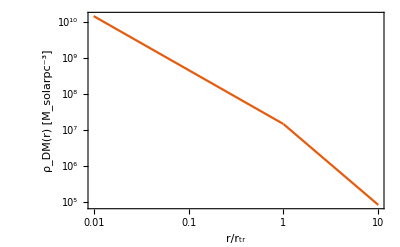

```mathematica
LogLogPlot[ρDM[x*rtr], {x,0.01 , 10}, PlotTheme->"Scientific",BaseStyle->{FontSize->14}, FrameLabel->{"r/r_tr", "ρ_DM(r) [M_solarpc^-3]"}]
```

#### Radial PDF

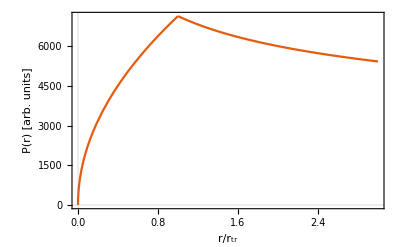

```mathematica
Plot[PDM[x*rtr], {x, 0, 3}, PlotRange->All,PlotTheme->"Scientific",BaseStyle->{FontSize->14}, FrameLabel->{"r/r_tr", "P(r) [arb. units]"}]
```

#### Enclosed Mass

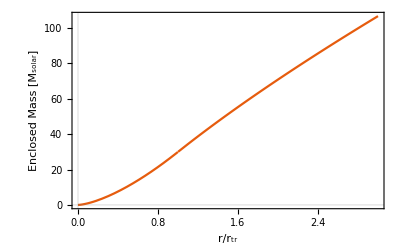

```mathematica
Plot[MencDM[x*rtr], {x, 0, 3},PlotTheme->"Scientific",BaseStyle->{FontSize->14}, FrameLabel->{"r/r_tr", "Enclosed Mass [M_solar]"}]
```

#### Velocity Dispersion

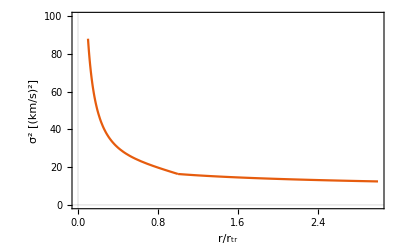

```mathematica
Plot[σsq[x*rtr], {x, 0.1, 3},PlotRange->{0,100},PlotTheme->"Scientific",BaseStyle->{FontSize->14}, FrameLabel->{"r/r_tr", "σ^2 [(km/s)^2]"}]
```

### Eddington’s Formula

```mathematica
Φ[r_]=Assuming[ r ≥ 0 && rtr > 0, Integrate[- G Menc[x]/x^2, {x, r, Infinity}]]
```

Piecewise[{{-(8 G MPBH)/rtr, r<0||(r≤0&&r-rtr≥0)||r-rtr==0||(r-rtr≥0&&rtr≤0)}, {-(8 G MPBH)/(r^(1/4) rtr^(3/4)), r>0&&r-rtr>0&&rtr>0}, {(G MPBH (2 r^(3/2)-9 r √rtr-rtr^(3/2)))/(r rtr^(3/2)), True}}]

```mathematica
Φ1[r_] = Assuming[r > rtr, Integrate[- G Menc[x]/x^2, {x, r, Infinity}]]
```

-(8 G MPBH)/((r rtr^3)^(1/4))

```mathematica
Φ2[r_] = FullSimplify[Assuming[0 ≤ r ≤ rtr, Integrate[- G Menc[x]/x^2, {x, r, rtr}]] + Φ1[rtr]]
```

-(8 G MPBH)/rtr+(Piecewise[{{(G MPBH (2 r^(3/2)-r √rtr-rtr^(3/2)))/(r rtr^(3/2)), r>0&&r-rtr<0}, {0, r-rtr≥0&&r>0}, {Integrate[-(G (MPBH+4 π (Piecewise[{{MPBH/(4 π), -rtr+x==0&&x>0}, {(MPBH (-1+(2 x^(3/4))/rtr^(3/4)))/(4 π), -rtr+x>0&&x>0}, {(MPBH x^(3/2))/(4 π rtr^(3/2)), -rtr+x<0&&x>0}, {0, True}}])))/x^2,{x,r,rtr},Assumptions→rtr∈Reals&&r==0&&rtr>0&&r-rtr≤0], True}}])

```mathematica
ClearAll[ψ]
ψ[r_]:= -Φ[r]
```

```mathematica
ClearAll[rtr, MPBH,G]
```

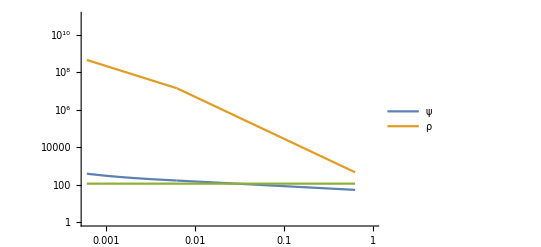

```mathematica
MPBH = 30;
rtr = 0.0063;
G = 4.302 10^-3;
LogLogPlot[{ψ[r], ρDM[r], 111.63},{r,0,  100rtr}, PlotLegends->{ψ, ρ}, PlotRange->{1, 10^11}]
```

```mathematica
invA[ψ1_]=x/.Solve[ψ[x] == ψ1 , x][[1]]
invB[ψ1_]=x/.Solve[ψ[x] == ψ1 , x][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ConditionalExpression[(4.5447×10^6)/Re[ψ1]^4,0<Re[ψ1]<163.886&&Im[ψ1]==0]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ConditionalExpression[Root[-5.54704×10^43+(-1.58487×10^47+8.59606×10^44 Re[ψ1]) #1+(-1.13205×10^50+1.22801×10^48 Re[ψ1]-3.33026×10^45 Re[ψ1]^2) #1^2+8.87359×10^50 #1^3&,1],Re[ψ1]>163.886&&Im[ψ1]==0]

```mathematica
inv[ψ1_] := Piecewise[{{invA[ψ1], 0 ≤ ψ1 ≤ ψ[rtr]},{invB[ψ1], ψ1 > ψ[rtr]}}]
```

```mathematica
inv[1000]
```

0.000156989

```mathematica
ClearAll[ρofψ]
ρofψ[ψ1_] = ρDM[inv[ψ1]];
```

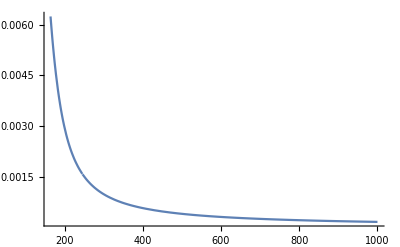

```mathematica
Plot[inv[ψ1], {ψ1, 0, 1000}, PlotRange->All]
```

```mathematica
ψ[rtr+10^-15]
```

163.886

```mathematica
ρofψ''[100]
```

1209.05

```mathematica
ρofψ[ψ1]
```

ConditionalExpression[Piecewise[{{7161.3/(Piecewise[{{(4.5447×10^6)/Re[ψ1]^4, 0≤ψ1≤163.886}, {Root[-5.54704×10^43+(-1.58487×10^47+8.59606×10^44 Re[ψ1]) #1+(-1.13205×10^50+1.22801×10^48 Re[ψ1]-3.33026×10^45 Re[ψ1]^2) #1^2+8.87359×10^50 #1^3&,1], ψ1>163.886}, {0, True}}])^(3/2), (Piecewise[{{(4.5447×10^6)/Re[ψ1]^4, 0≤ψ1≤163.886}, {Root[-5.54704×10^43+(-1.58487×10^47+8.59606×10^44 Re[ψ1]) #1+(-1.13205×10^50+1.22801×10^48 Re[ψ1]-3.33026×10^45 Re[ψ1]^2) #1^2+8.87359×10^50 #1^3&,1], ψ1>163.886}, {0, True}}])≤0.0063}, {160.139/(Piecewise[{{(4.5447×10^6)/Re[ψ1]^4, 0≤ψ1≤163.886}, {Root[-5.54704×10^43+(-1.58487×10^47+8.59606×10^44 Re[ψ1]) #1+(-1.13205×10^50+1.22801×10^48 Re[ψ1]-3.33026×10^45 Re[ψ1]^2) #1^2+8.87359×10^50 #1^3&,1], ψ1>163.886}, {0, True}}])^(9/4), (Piecewise[{{(4.5447×10^6)/Re[ψ1]^4, 0≤ψ1≤163.886}, {Root[-5.54704×10^43+(-1.58487×10^47+8.59606×10^44 Re[ψ1]) #1+(-1.13205×10^50+1.22801×10^48 Re[ψ1]-3.33026×10^45 Re[ψ1]^2) #1^2+8.87359×10^50 #1^3&,1], ψ1>163.886}, {0, True}}])>0.0063}, {0, True}}],(Im[ψ1]==0&&0<Re[ψ1]<163.886&&ψ1≤163.886)||(Im[ψ1]==0&&Re[ψ1]>163.886&&ψ1>163.886)||ψ1<0]

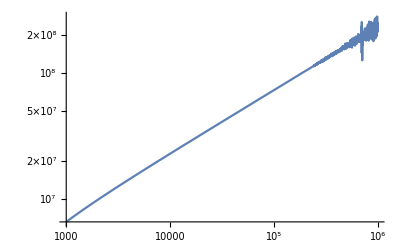

```mathematica
LogLogPlot[ND[ρofψ[s], {s,1},ψ1], {ψ1, 10^3, 10^6}, PlotRange->All]
```

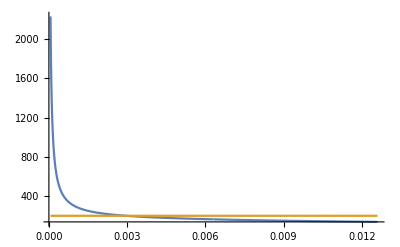

```mathematica
Plot[{ψ[r], 200}, {r, 0.01 rtr, 2 rtr}, PlotRange->All]
```

```mathematica
ψ[10^-5 rtr]
```

2.04876×10^6

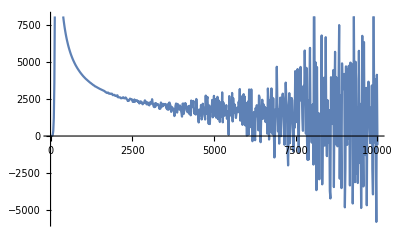

```mathematica
Plot[ND[ρofψ[s],{s,2},ψ1], {ψ1, 0, 10000}, PlotPoints->10]
```

```mathematica
f[ϵ_]:=(1/(Sqrt[8] π^2))(NIntegrate[ND[ρofψ[s],{s,2},ψ1]/Sqrt[ϵ - ψ1], {ψ1, 0, ϵ}])
```

```mathematica
f[10000]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {9834.3060905430367029111948795616626739501953125}. NIntegrate obtained 151656. and 34024.7 for the integral and error estimates.

5432.7

```mathematica
f[5000]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {171.394}. NIntegrate obtained 374247. and 2868.63 for the integral and error estimates.

13406.4

```mathematica
f[1000]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {164.047}. NIntegrate obtained 344640. and 27304.6 for the integral and error estimates.

12345.9

```mathematica
ftab = Table[{PrintTemporary[e1];e1, f[e1]}, {e1,Linspace[0, 100, 21]}]
```

{{0,0.},{5,4.81599×10^-8},{10,8.71787×10^-6},{15,0.000182429},{20,0.0015781},{25,0.00841318},{30,0.0330232},{35,0.104935},{40,0.285667},{45,0.691041},{50,1.52295},{55,3.11265},{60,5.97784},{65,10.8958},{70,18.9953},{75,31.8691},{80,51.7113},{85,81.4802},{90,125.092},{95,187.645},{100,275.683}}

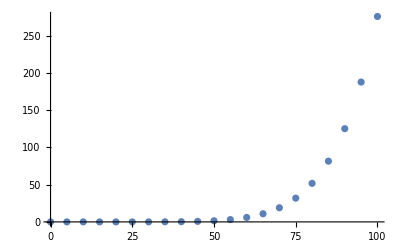

```mathematica
ListPlot[ftab]
```

```mathematica
Plot[ρofψ''[ψ1], {ψ1, 0, 10}, PlotPoints->2]
```

$Aborted

```mathematica
Sqrt[σsq[0.1 rtr]]
```

9.38255

```mathematica
finterp = Interpolation[ftab]
```

InterpolatingFunction[{{0., 100.}}, <>]

NIntegrate::inumr: The integrand ((1171.02 HeavisideTheta[-0.0063+ψ^((«1»«1»)[ψ1]])/((«1»)^2 (ψ^(-1)[ψ1])^(17/4))+«10»+(7161.3 «1»«1»(«1»))/((«1»)^2 («1»«1»«2»])^(3/2)))/(√(326.272-ψ1)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{244.704,326.272}}.

NIntegrate[ρofψ''[ψ1]/(√(326.272-ψ1)),{ψ1,0,326.272}]/(2 √2 π^2)

```mathematica
ψ[10^-5]
```

13088.7

```mathematica
Plot[f[ϵ1], {ϵ1, 0, 1000}, PlotPoints->2]
```

$Aborted

```mathematica
ψ[0.1 rtr]
```

376.272

```mathematica
xpos = 10^-3;
```

```mathematica
Normy = NIntegrate[ v^2 finterp[ψ[xpos rtr] - 0.5*v^2], {v, 0, 200}]
```

3.23478×10^16

```mathematica
Sqrt[NIntegrate[v^4finterp[ψ[xpos rtr] - 0.5*v^2], {v, 0, 200}]/Normy]
```

105.984

```mathematica
Sqrt[σsq[xpos rtr]]
```

90.5259

InterpolatingFunction::dmval: Input value {20668.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

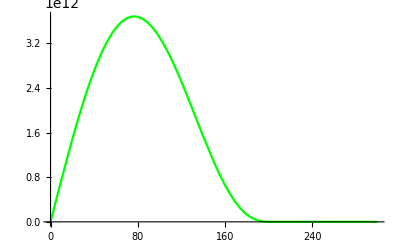

```mathematica
A1 = Plot[v finterp[ψ[xpos rtr] - 0.5*v^2], {v, 0, 300}, PlotPoints->2, PlotRange->All, PlotStyle->Green]
```

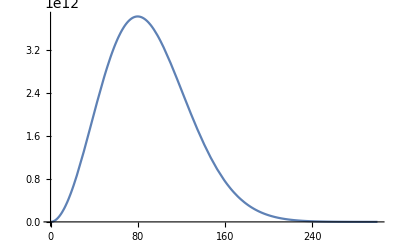

```mathematica
B1 =Plot[ 2.3 10^11 x^2 PDF[NormalDistribution[0,Sqrt[ 0.39 σsq[xpos rtr]]]][x],{x, 0, 300}]
```

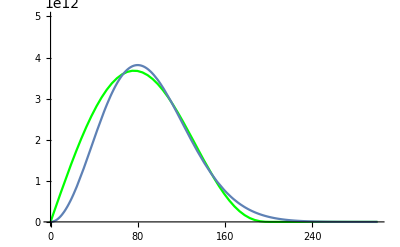

```mathematica
Show[A1, B1, PlotRange->{0, 5 10^12}]
```

### Solving Eddington’s Equation - v2

```mathematica
ClearAll[S]
S[x_] := B(1 + x^-1 - 2 Sqrt[x])
```

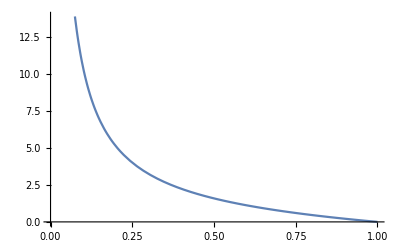

```mathematica
Plot[{S[x]/B}, {x, 0, 1}]
```

```mathematica
xinv[S1_]=x/.Assuming[S1 ≥ 0 && B > 0 && S1 ∈ Reals && B ∈ Reals ,
Simplify[Solve[S[x] == S1 ,x,Reals][[1]]]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Root[-514089.+(-1.02818×10^6+50190. S1) #1+(-514089.+50190. S1-1225. S1^2) #1^2+2.05636×10^6 #1^3&,1]

```mathematica
ClearAll[A,B]
MPBH = 30;
rtr = 0.0063;
G = 4.302 10^-3;
A = 3 MPBH/(8 π rtr^3);
B = G MPBH/rtr;
```

```mathematica
ρDM2[x_]:= A x^(-3/2)
```

```mathematica
ClearAll[ρofψ]
ρofψ[ψ1_]:= ρDM2[ xinv[ψ1]]
```

```mathematica
ρofψ[a]
```

(1.43213×10^7)/(Root[-514089.+(-1.02818×10^6+50190. a) #1+(-514089.+50190. a-1225. a^2) #1^2+2.05636×10^6 #1^3&,1]^(3/2))

LogLogPlot::prng: Value of option PlotRange -> {2.03952×10^7} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

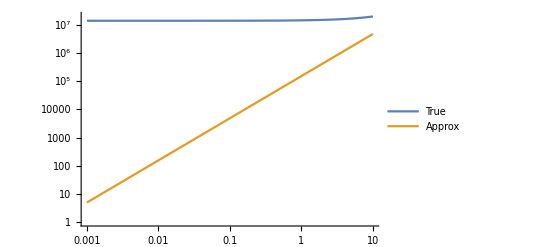

```mathematica
amax = 10;
LogLogPlot[{ρofψ[a], (A/B^(3/2))a^(3/2)}, {a, 0.001, amax}, PlotLegends->{"True", "Approx"}, PlotRange->{ ρofψ[amax]}]
```

```mathematica
ρp[ψ1_]:= (3/2)A (ψ1-B)^(1/2)/B^(3/2)
ρpp[ψ1_]:= (3/4)A (ψ1-B)^(-1/2)/B^(3/2)
```

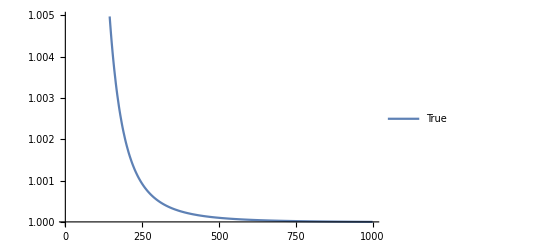

```mathematica
amax=1000;
Plot[{ND[ρofψ[x], {x,1}, a]/ρp[a]} , {a, 1, amax}, PlotLegends->{"True", "Approx"}]
```

1000

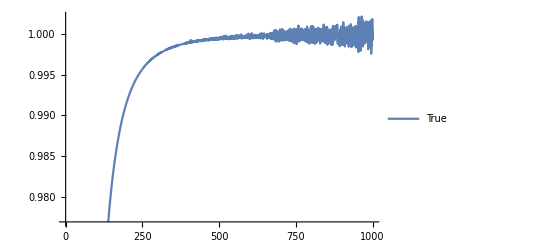

```mathematica
amax=1000
Plot[{ND[ρofψ[x], {x,2}, a]/ρpp[a]} , {a, 0, amax}, PlotLegends->{"True", "Approx"}]
```

```mathematica
Root[-B^2+(-6 B^2+2 B S1) #1^2+(-9 B^2+6 B S1-S1^2) #1^4+4 B^2 #1^5&,1]
```

Root[-419.664+(-2517.99+40.9714 S1) #1^2+(-3776.98+122.914 S1-S1^2) #1^4+1678.66 #1^5&,1]

```mathematica
d2ρ[ψ1_]:= Piecewise[{{ND[ρofψ[x], {x,2}, ψ1], ψ1 < 500},{ρpp[ψ1], ψ1≥ 500}}]
```

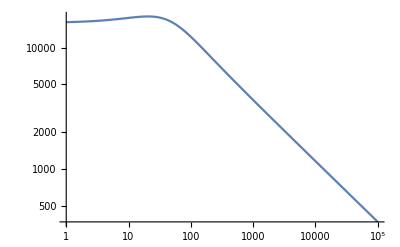

```mathematica
LogLogPlot[Abs[d2ρ[a]] , {a, 1, 100000}]
```

```mathematica
(A/B)*(3/4)
```

524314.

```mathematica
A
```

1.43213×10^7

```mathematica
ND[ρofψ[x], {x,1}, 0]
```

524314.

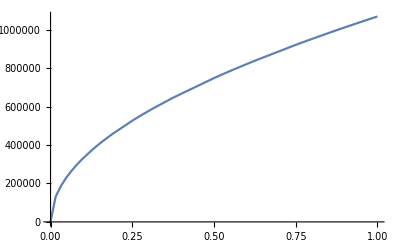

```mathematica
Plot[NIntegrate[ND[ρofψ[x], {x,1}, s]/Sqrt[ϵ - s], {s, 0, ϵ}], {ϵ, 0, 1}, PlotPoints->2]
```

```mathematica
f[ϵ_]:=(1/(Sqrt[8] π^2))(NIntegrate[d2ρ[ψ1]/Sqrt[ϵ - ψ1], {ψ1, 0, ϵ}] +(ND[ρofψ[x], {x,1}, 0]) /Sqrt[ϵ])
```

```mathematica
MPBH = 30;
rtr = 0.0063;
G = 4.302 10^-3;
A = 3 MPBH/(8 π rtr^3);
B = G MPBH/rtr;
```

```mathematica
vmax[xpos_]:= Sqrt[ 2 (S[xpos] )];
```

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {355.344}. NIntegrate obtained 334953. and 0.383373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {407.976559054373137058746578986756503582000732421875}. NIntegrate obtained 336591.-4.29621×10^-6 ⅈ and 0.382446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {443.3875814754357289615427362150512635707855224609375}. NIntegrate obtained 337312.-3.24396×10^-6 ⅈ and 0.651258 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

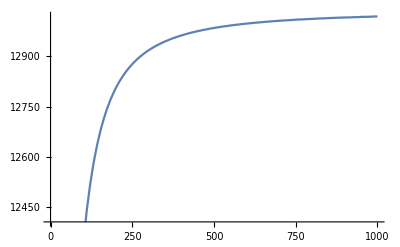

```mathematica
ϵvals = Linspace[0, 1000, 100];
ftab = Table[{ϵ, f[ϵ]}, {ϵ, ϵvals}];
finterp = Interpolation[ftab, InterpolationOrder->1];
Plot[finterp[ϵ], {ϵ, 0, 1000}]
```

```mathematica
Plot[finterp[ϵ], {ϵ, 0, 1000}]
```

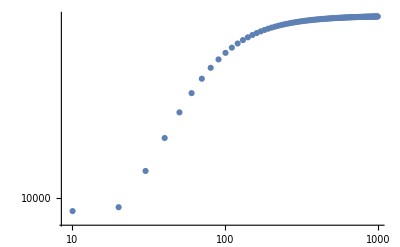

```mathematica
ListLogLogPlot[ftab]
```

```mathematica
lfinterp = Interpolation[lftab, InterpolationOrder->1];
finterp = Interpolation[10^lftab, InterpolationOrder->1];
ffunc[ϵ_]:= Piecewise[{{10^lfinterp[Log10[ϵ]] , ϵ < 999},{10^lfinterp[2.9], ϵ ≥ 999}}]
ffunc2[ϵ_]:= Piecewise[{{finterp[ϵ] , ϵ < 999},{finterp[999], ϵ ≥ 999}}]
```

```mathematica
ψinv[0.5]
```

5.56621×10^9

```mathematica
Dens[xpos_]:= 4 π NIntegrate[v^2 finterp[S[xpos] - 0.5*v^2], {v, 0, vmax[xpos]}]
```

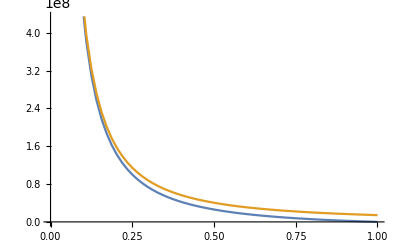

```mathematica
L1 = Plot[{(Dens[x]),ρDM2[x]}, {x, 0, 1}, PlotPoints->2]
```

4.37871

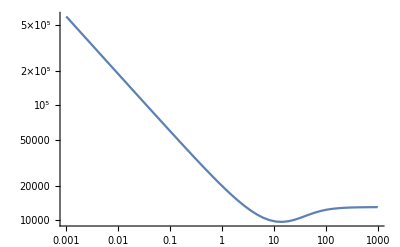

0.146243

```mathematica
xpos = 0.9;
S[xpos]
LogLogPlot[ffunc[ϵ], {ϵ, 10^-3,1000}]
4 π NIntegrate[v^2 ffunc[S[xpos] - 0.5*v^2], {v, 0, vmax[xpos]}]/ρDM2[xpos]
```

```mathematica
Moments[n_]:=4π NIntegrate[v^(2+n) ffunc[S[xpos] - 0.5*v^2], {v, 0,  vmax[xpos]}]
 Sqrt[(Moments[2])/Moments[0]]/Sqrt[3]
```

1.46362

### Solving Eddington’s Equation - v3

```mathematica
ClearAll[A,B]
MPBH = 30;
rtr = 0.0063;
G = 4.302 10^-3;
A = 3 MPBH/(8 π rtr^3);
B = G MPBH/rtr;
```

DM density profile

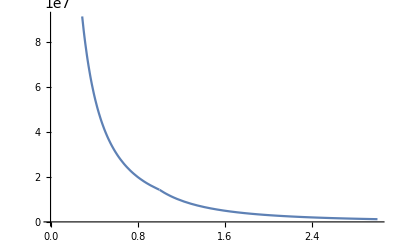

```mathematica
ClearAll[ρDM]
ρDM[x_]:= Piecewise[{{A x^(-3/2), x < 1},{A  x^(-9/4), x≥ 1}}]
ρinner[x_]:= A x^(-3/2)
ρouter[x_]:=A x^(-9/4)
Plot[ρDM[x], {x, 0, 3}]
```

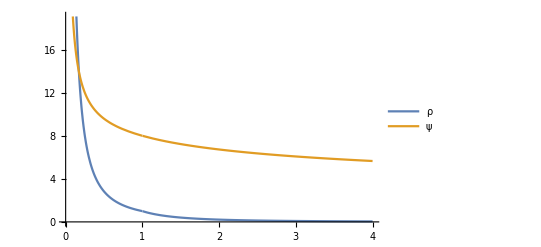

```mathematica
ClearAll[ϕ, ψ]
Menc[x_]:= Piecewise[{{2 MPBH x^(3/4), x >= 1},{MPBH (1+x^(3/2)), x < 1}}]
ϕ[x_] := Piecewise[{{-8B x^(-1/4),x ≥1},{-B(9 + x^-1 - 2 x^(1/2)),x < 1}}]
ψ[x_] := Piecewise[{{8B x^(-1/4),x ≥1},{B(9 + x^-1 - 2 x^(1/2)),x < 1}}]
ψinner[x_] := B(9 + x^-1 - 2 x^(1/2));
ψouter[x_]:=8B x^(-1/4);
ψtr = ψ[1];
ρtr = ρDM[1];
Plot[{ρDM[x]/A,ψ[x]/B}, {x, 0, 4}, PlotLegends->{"ρ", "ψ"}]
```

```mathematica
ψinvOuter[ψ1_]:= (ψ1/(8 B))^-4
ψinvInner[ψ1_]=x/.Assuming[ψ1 ≥ 0 && B > 0 && ψ1 ∈ Reals && B ∈ Reals ,
Simplify[Solve[ψinner[x] == ψ1 ,x,Reals][[1]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Root[-514089.+(-9.2536×10^6+50190. ψ1) #1+(-4.16412×10^7+451710. ψ1-1225. ψ1^2) #1^2+2.05636×10^6 #1^3&,1]

```mathematica
ψinv[ψ1_]:= Piecewise[{{ψinvOuter[ψ1], ψ1 < ψtr},{ψinvInner[ψ1], ψ1 ≥ ψtr}}]
```

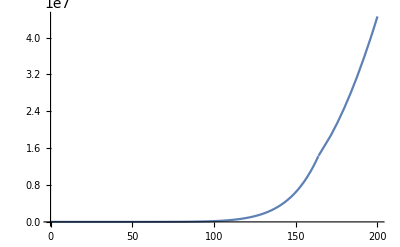

```mathematica
ρofψ[ψ1_]:= ρDM[ψinv[ψ1]]
Plot[ρofψ[ψ1], {ψ1, 0, 200}]
```

Asymptotic derivatives

```mathematica
ClearAll[dρAsymp, d2ρAsymp]
dρAsymp[ψ1_]:= (3/2)A (ψ1 - 9 B)^(1/2)/B^(3/2)
d2ρAsymp[ψ1_]:= (3/4)A (ψ1-9B)^(-1/2)/B^(3/2)
```

```mathematica
ClearAll[d2ρ]
d2ρ[ψ1]:= Piecewise[{
{ND[ρofψ[a], {a, 2}, ψtr - 0.5], ψtr - 0.5< ψ1 ≤ ψtr},
{ND[ρofψ[a], {a, 2}, ψtr + 0.5], ψtr < ψ1 ≤ ψtr+0.5},
{ND[ρofψ[a], {a, 2}, ψ1], ψ1 < 1000},
{d2ρAsymp[ψ1], ψ1 ≥1000}}
]
```

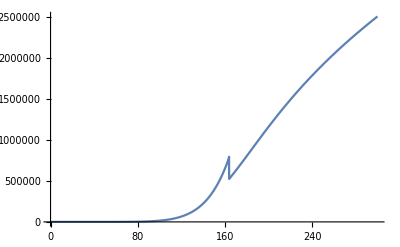

```mathematica
Plot[ND[ρofψ[a], {a, 1}, ψ1], {ψ1, 0, 300}]
```

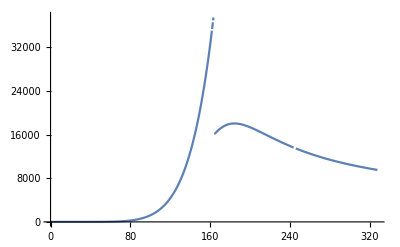

```mathematica
Plot[d2ρ[ψ1], {ψ1, 0, 2 ψtr}]
```

Calculating the discontinuity as x = 1

```mathematica
dinner = D[ρinner[x], x]/D[ψinner[x],x]/.x->1
douter = D[ρouter[x], x]/D[ψouter[x],x]/.x->1
jump = -douter + dinner
```

524314.

786470.

-262157.

```mathematica
f[ϵ_]:=If[ϵ < ψtr, 
(1/(Sqrt[8] π^2))(NIntegrate[d2ρ[ψ1]/Sqrt[ϵ - ψ1], {ψ1, 0, ϵ}]),
(1/(Sqrt[8] π^2))(NIntegrate[d2ρ[ψ1]/Sqrt[ϵ - ψ1], {ψ1, 0,ϵ}]  + jump/Sqrt[ϵ - ψtr])];
```

```mathematica
f[0]
```

0.

{0.,4.04835,8.0967,12.1451,16.1934,20.2418,24.2901,28.3385,32.3868,36.4352,40.4835,44.5319,48.5802,52.6286,56.6769,60.7253,64.7736,68.822,72.8703,76.9187,80.967,85.0154,89.0637,93.1121,97.1604,101.209,105.257,109.305,113.354,117.402,121.451,125.499,129.547,133.596,137.644,141.692,145.741,149.789,153.837,157.886,158.886,159.412,159.938,160.465,160.991,161.517,162.044,162.57,163.096,163.623,163.786,163.986,164.149,164.675,165.202,165.728,166.254,166.78,167.307,167.833,168.359,168.886,169.886,210.526,260.889,323.3,400.641,496.484,615.254,762.438,944.831,1170.86,1450.95,1798.05,2228.19,2761.23,3421.78,4240.35,5254.74,6511.8,8069.57,10000.}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {163.8516829520304434464339493615625542588531970977783203125}. NIntegrate obtained 299604. and 248.297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {163.86117399243941716857619894653907977044582366943359375}. NIntegrate obtained 293316. and 268.644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {163.877263881434}. NIntegrate obtained 283131. and 157.274 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

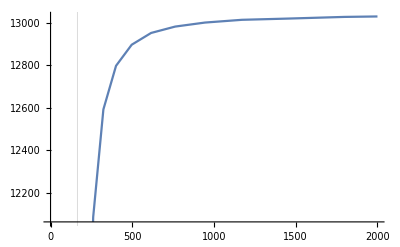

```mathematica
ϵmin = 0; ϵmax = 2000;
ϵvals = Sort[N[Flatten[{ Linspace[ψtr - 5, ψtr + 5,20],Linspace[0, ψtr-6, 40], ψtr-0.1, ψtr + 0.1, 10^Linspace[Log10[ψtr+6], Log10[10000], 20]}]]]
(*ϵvals = Linspace[ψtr - 5, ψtr + 5, 50];*)
ftab = Table[{ϵ, Clip [f[ϵ], {0, 10^30}]}, {ϵ, ϵvals}];
finterp = Interpolation[ftab, InterpolationOrder->1];
Plot[finterp[ϵ], {ϵ, ϵmin, ϵmax}, GridLines->{{ ψtr},{}}]
```

```mathematica
Log10[ftab]
```

{{-5.,-20.0338},{0.607279,-8.005},{0.908309,-5.74727},{1.0844,-4.42659},{1.20934,-3.48955},{1.30625,-2.76273},{1.38543,-2.16887},{1.45238,-1.66677},{1.51037,-1.23183},{1.56152,-0.848184},{1.60728,-0.505002},{1.64867,-0.194557},{1.68646,0.0888568},{1.72122,0.349573},{1.75341,0.590958},{1.78337,0.815682},{1.8114,1.0259},{1.83773,1.22336},{1.86255,1.40954},{1.88603,1.58565},{1.90831,1.75272},{1.9295,1.91164},{1.9497,2.06317},{1.96901,2.20796},{1.98749,2.34658},{2.00522,2.47955},{2.02225,2.6073},{2.03864,2.73023},{2.05444,2.84868},{2.06968,2.96298},{2.0844,3.07341},{2.09864,3.18021},{2.11243,3.28362},{2.12579,3.38385},{2.13876,3.48109},{2.15135,3.57551},{2.16358,3.66727},{2.17548,3.75651},{2.18706,3.84337},{2.19834,3.92798},{2.20108,3.94855},{2.20252,3.95932},{2.20395,3.97005},{2.20538,3.98076},{2.2068,3.99142},{2.20822,4.00205},{2.20963,4.01265},{2.21104,4.02321},{2.21244,4.03378},{2.21384,4.0441},{2.21428,4.04696},{2.21481,4.27795+1.36438 ⅈ},{2.21524,3.89206+1.36438 ⅈ},{2.21663,2.63033+1.36438 ⅈ},{2.21801,3.24612},{2.2194,3.46473},{2.22077,3.56171},{2.22215,3.62014},{2.22351,3.6611},{2.22488,3.68993},{2.22624,3.71447},{2.22759,3.73363},{2.23016,3.76241},{2.32331,4.02615},{2.41646,4.08222},{2.50961,4.10009},{2.60276,4.10712},{2.69591,4.11048},{2.78905,4.11235},{2.8822,4.11335},{2.97535,4.11398},{3.0685,4.11442},{3.16165,4.11461},{3.2548,4.11487},{3.34795,4.11502},{3.4411,4.11493},{3.53425,4.11511},{3.6274,4.11505},{3.72055,4.11497},{3.8137,4.11529},{3.90685,4.11523},{4.,4.11532}}

```mathematica
ϵvals
```

{0.00001,4.04836,8.09671,12.1451,16.1934,20.2418,24.2901,28.3385,32.3868,36.4352,40.4835,44.5319,48.5802,52.6286,56.6769,60.7253,64.7736,68.822,72.8703,76.9187,80.967,85.0154,89.0637,93.1121,97.1604,101.209,105.257,109.305,113.354,117.402,121.451,125.499,129.547,133.596,137.644,141.692,145.741,149.789,153.837,157.886,158.886,159.412,159.938,160.465,160.991,161.517,162.044,162.57,163.096,163.623,163.786,163.986,164.149,164.675,165.202,165.728,166.254,166.78,167.307,167.833,168.359,168.886,169.886,210.526,260.889,323.3,400.641,496.484,615.254,762.438,944.831,1170.86,1450.95,1798.05,2228.19,2761.23,3421.78,4240.35,5254.74,6511.8,8069.57,10000.}

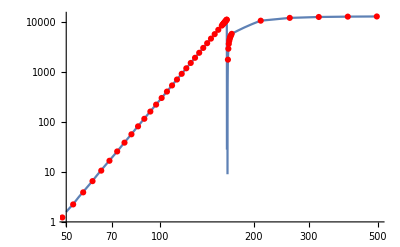

```mathematica
Show[LogLogPlot[finterp[ϵ], {ϵ, 50, 500}], ListLogLogPlot[ftab, PlotStyle->Red]]
```

```mathematica
ClearAll[vmax]
vmax[xpos_]:= Sqrt[ 2 (ψ[xpos] )];
```

```mathematica
Dens[xpos_]:= 4 π NIntegrate[v^2 finterp[ψ[xpos] - 0.5*v^2], {v, 0, vmax[xpos]}]
```

```mathematica
xpos = 10.0
ψ[xpos]
Dens[xpos]
ρDM[xpos]
```

10.

92.1597

81473.8

80534.3

```mathematica
LogPlot[{ Dens[x], ρDM[x]}, {x, 0.01, 5}, PlotRange-> All, PlotLegends->{"Reconstructed", "True"},
 PlotTheme->"Scientific", FrameLabel->{"x = r/r_tr", "ρ(x)"}, ImageSize->500]
```

$Aborted

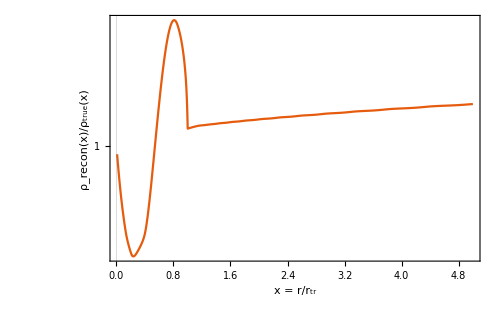

```mathematica
LogPlot[{ Dens[x]/ρDM[x]}, {x, 0.01, 5}, PlotRange-> All,
 PlotTheme->"Scientific", FrameLabel->{"x = r/r_tr", "ρ_recon(x)/ρ_true(x)"}, ImageSize->500]
```

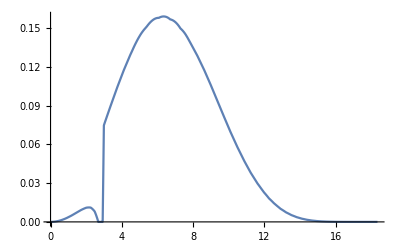

```mathematica
xpos =0.9;
Plot[{ 4π v^2 finterp[ψ[xpos] - 0.5*v^2]/ρDM[xpos]}, {v, 0, vmax[xpos]}]
```

```mathematica
A^(1/2)
```

3784.34

```mathematica
sig[x_]:= Sqrt[ 4 π NIntegrate[v^4 finterp[ψ[x] - 0.5*v^2],{v, 0, vmax[x]}] /ρDM[x]]
```

```mathematica
N[Sqrt[3]]
N[Sqrt[4π]]
```

1.73205

3.54491

```mathematica
Print[sig[0.1]]
```

16.1183

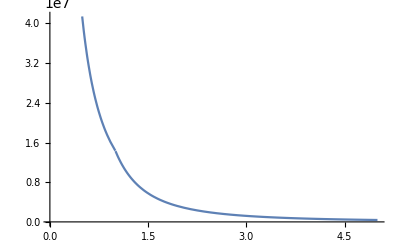

```mathematica
Plot[ρDM[x], {x, 0.01, 5}]
```

```mathematica
Plot[sig[x]/Sqrt[3], {x, 0.01, 5}, PlotRange->{0, 20}]
```

$Aborted

```mathematica
ftab
```

{{0.,0.},{4.04835,9.88546×10^-9},{8.0967,1.78946×10^-6},{12.1451,0.0000374461},{16.1934,0.000323927},{20.2418,0.00172692},{24.2901,0.00677846},{28.3385,0.0215393},{32.3868,0.058637},{36.4352,0.141846},{40.4835,0.312606},{44.5319,0.638914},{48.5802,1.22703},{52.6286,2.23652},{56.6769,3.89904},{60.7253,6.54156},{64.7736,10.6144},{68.822,16.7249},{72.8703,25.6768},{76.9187,38.5167},{80.967,56.5877},{85.0154,81.5909},{89.0637,115.656},{93.1121,161.419},{97.1604,222.117},{101.209,301.68},{105.257,404.853},{109.305,537.31},{113.354,705.801},{117.402,918.294},{121.451,1184.15},{125.499,1514.29},{129.547,1921.42},{133.596,2420.2},{137.644,3027.53},{141.692,3762.77},{145.741,4648.},{149.789,5708.34},{153.837,6972.27},{157.886,8471.91},{158.886,8882.73},{159.412,9105.81},{159.938,9333.72},{160.465,9566.56},{160.991,9804.42},{161.517,10047.4},{162.044,10295.5},{162.57,10549.},{163.096,10808.8},{163.623,11068.7},{163.786,11142.},{163.986,0},{164.149,0},{164.675,0},{165.202,1762.48},{165.728,2915.59},{166.254,3645.12},{166.78,4170.},{167.307,4582.45},{167.833,4896.98},{168.359,5181.7},{168.886,5415.38},{169.886,5786.37},{210.526,10620.7},{260.889,12084.3},{323.3,12591.7},{400.641,12797.3},{496.484,12896.7},{615.254,12952.2},{762.438,12982.3},{944.831,13001.2},{1170.86,13014.2},{1450.95,13020.},{1798.05,13027.9},{2228.19,13032.4},{2761.23,13029.7},{3421.78,13034.9},{4240.35,13033.2},{5254.74,13030.8},{6511.8,13040.5},{8069.57,13038.6},{10000.,13041.4}}

```mathematica
Export[NotebookDirectory[] <> "Distribution.dat", ftab, "Table"]
```

/Users/bradkav/Projects/PBH_dress/PBHinDMclothing/code/Distribution.dat

### Solving Eddington’s Equation - v4

Exponential cut off

```mathematica
ClearAll[A,B]
MPBH = 30;
rtr = 0.0063*(MPBH^(1/3));
G = 4.302 10^-3;
A = 3 MPBH/(8 π rtr^3);
B = G MPBH/rtr;
```

DM density profile

```mathematica
ClearAll[ρDM, α, β,α2, β2]
ρinner[x_]:= A x^(-3/2)
ρouter[x_]:= α + β x-(4.5 10^6)x^2
(*ρouter[x_]:= α(1 + β x-100 x^2)*)
j1= 0.9;
j2 = 1.1;
ρextra[x_]:=α2 Exp[-(x-j2)/β2]
(*Solve for α and β to get continuous ρ and ρ'*)
s = Solve[ρinner[j1] == ρouter[j1] && ρinner'[j1] == ρouter'[j1], {α, β}];
α = s[[All,1,2]][[1]]
β = s[[All,2,2]][[1]]

s2 = Solve[ρextra[j2] == ρouter[j2] && ρextra'[j2] == ρouter'[j2], {α2, β2}];
α2 = s2[[All,1,2]][[1]]
β2 = s2[[All,2,2]][[1]]
ρDM[x_]:= Piecewise[{{ρinner[x], x < j1},{ρouter[x], j1 <=x <= j2}, {ρextra[x], x > j2}}]
```

-2.24723×10^6

7.16815×10^6

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

192739.

0.0705526

```mathematica
ρDM[0.9]
```

559108.

```mathematica
1.1
```

1.1

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.36925×10^6

0.909091

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -14106536370349316+9404357580232877 Log[ⅇ^(1/β)] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2.13945×10^6

0.666667

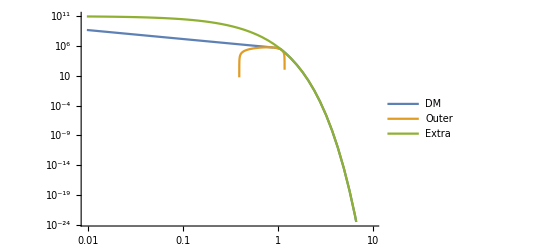

```mathematica
LogLogPlot[{ρDM[x],ρouter[x],ρextra[x]}, {x, 0, 10}, PlotLegends->{"DM","Outer", "Extra"}]
```

Potentials

```mathematica
ClearAll[ ψ, Minner, Mouter,Menc, ψouter, ψinner]
Minner[x_]:=MPBH (1+x^(3/2));
(*Mouter[x_]=2MPBH + rtr^3 Integrate[4 π ρouter[x1] x1^2, {x1, 1, x}];*)
(*Menc[x_] :=  Piecewise[{{Mouter[x], x >= 1},{Minner[x], x < 1}}]*)
Menc[x_] = Assuming[{x > 0},rtr^3 Integrate[4 π ρDM[x1] x1^2, {x1, 0, x}]]
(*ψouter[x_]= G Assuming[ x > 1, rtr^-1 Integrate[Mouter[x1]/x1^2, {x1, x, ∞}]];
ψinner[x_] = ψouter[1] + B(1 + x^-1 - 2 x^(1/2));
ψ[x_] := Piecewise[{{ψouter[x],x ≥1},{ψinner[x],x < 1}}]*)
ψtr = ψ[1];
ρtr = ρDM[1];
```

7.50141×10^-6 (Piecewise[{{3.99925×10^6 x^(3/2), x≤0.9}, {1.03496×10^-18 (2.10648×10^24-9.09523×10^24 x^3+2.17588×10^25 x^4-1.09277×10^25 x^5), 0.9<x≤1.1}, {4.40742×10^6+4.63559×10^-14 (5.06925×10^18+100. ⅇ^(-1.41738 (-11.+10. x)) (-3.66981×10^14-1.91997×10^8 x (2.70917×10^7+1.91997×10^8 x))), True}}])

```mathematica
ψouter[x]
```

(0.219764 (39.3503+64.9915 Erf[0.866025 x]-31.755 x ExpIntegralEi[-0.75 x^2]-31.755 x Gamma[0,0.75 x^2]))/x

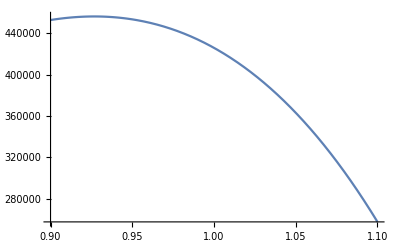

```mathematica
Plot[ρDM[x]x^2, {x, 0.9, 1.1}]
```

```mathematica
Menc[x]
```

7.50141×10^-6 (Piecewise[{{3.99925×10^6 x^(3/2), x≤1.}, {-1.86023×10^-13 (-1.79771×10^19+8.57145×10^19 x^3-1.56789×10^20 x^4+6.75527×10^19 x^5), 1.<x≤1.1}, {4.5857×10^6+2.20575×10^-11 ⅇ^(-0.482353 (11.+10. x)) (1.48362×10^19 ⅇ^(4.82353 x)-20152. (7.27901×10^15+2.90996×10^8 x (1.20657×10^8+2.90996×10^8 x))), True}}])

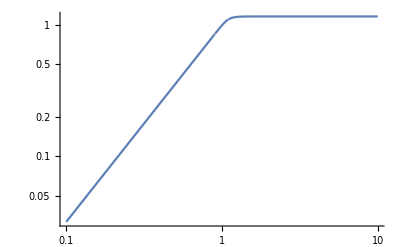

```mathematica
LogLogPlot[Menc[x]/MPBH, {x, 0.1, 10}, PlotRange->All]
```

```mathematica
Menc[1]
Menc[1.1]
Menc[1.25]
Menc[1.5]
```

29.8303

33.0619

34.5572

34.8137

```mathematica
LogPlot[{ψ[x]}, {x, 0, 5}, PlotLegends->{"ρ", "ψ"}, PlotRange->{10, 10^4}]
```

-Graphics-

Inverting the potentials

```mathematica
ψinvOuter[ψ1_]= x/.Assuming[1 ≤ x && ψ1 ≥ 0 && B > 0 && ψ1 ∈ Reals && B ∈ Reals ,
Simplify[Solve[ψouter[x] == ψ1 ,x,Reals]]]
ψinvInner[ψ1_]=x/.Assuming[ψ1 ≥ 0 && B > 0 && ψ1 ∈ Reals && B ∈ Reals ,
Simplify[Solve[ψinner[x] == ψ1 ,x,Reals][[1]]]]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {Solve[26.2643+19.6983 x+ⅇ^(1.5 x) (-34.4297+x Plus[«2»])==0,x,Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.Solve[26.2643+19.6983 x+ⅇ^(1.5 x) (-34.4297+x (2.18695×10^-15+1. ψ1))==0,x,Reals]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Root[-2.74124×10^47+(-2.55849×10^48+8.31572×10^46 ψ1) #1+(-5.96981×10^48+3.88067×10^47 ψ1-6.30656×10^45 ψ1^2) #1^2+1.0965×10^48 #1^3&,1]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ψtr
```

24.174

```mathematica
l  = ψinvOuter[ψtr - 10]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{2.26092}

```mathematica
l[[3]]
```

26.9541

```mathematica
ψinv[ψ1_]:= Piecewise[{{Last[ψinvOuter[ψ1]], ψ1 < ψtr},{ψinvInner[ψ1], ψ1 ≥ ψtr}}]
ρofψ[ψ1_]:= If[ψ1 == 0, 0, ρDM[ψinv[ψ1]]]
```

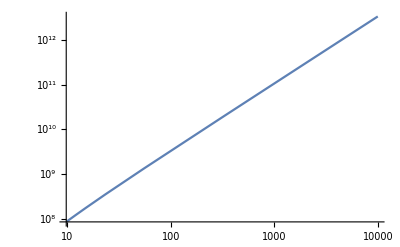

```mathematica
LogLogPlot[ρofψ[ψ1 ψtr], {ψ1, 0, 10000}, PlotPoints->2]
```

```mathematica
ρofψ[1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

7.96867×10^-17

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

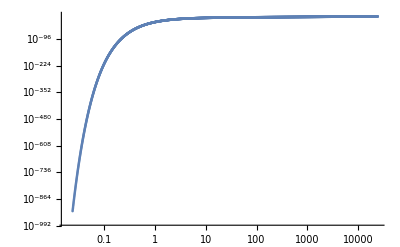

```mathematica
ψvals = ψtr DeleteDuplicates[Flatten[{0,10^Linspace[-3, 0, 1000],Linspace[0.9, 1.1, 100],10^Linspace[0,3,1000]}]];
ρtab = Table[{ψ1,ρofψ[ψ1]}, {ψ1,ψvals}];
ListLogLogPlot[ρtab]
```

```mathematica
ρofψinterp = Interpolation[ρtab];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

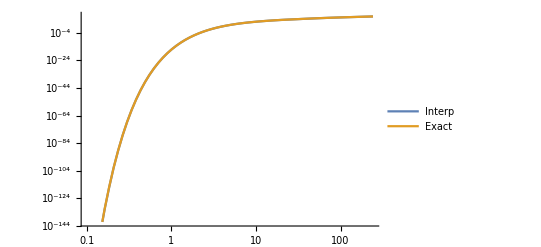

```mathematica
LogLogPlot[{ρofψinterp[ψ1], ρofψ[ψ1]}, {ψ1, 0.1, 10 ψtr}, PlotPoints->2, PlotLegends->{"Interp", "Exact"}]
```

Asymptotic derivatives

```mathematica
ClearAll[dρAsymp, d2ρAsymp]
dρAsymp[ψ1_]:= (3/2)A (ψ1 - (B+ ψ[1]))^(1/2)/B^(3/2)
d2ρAsymp[ψ1_]:= (3/4)A (ψ1-(B + ψ[1]))^(-1/2)/B^(3/2)
```

```mathematica
ClearAll[d2ρ]
d2ρ[ψ1]:= Piecewise[{
{ND[ρofψinterp[a], {a, 2}, ψ1], ψ1 < 10ψtr},
{d2ρAsymp[ψ1], ψ1 ≥10 ψtr}}
]
```

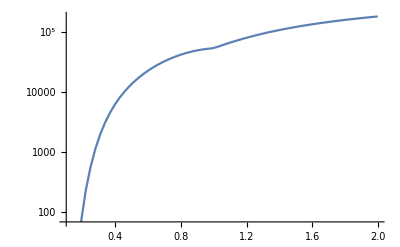

```mathematica
LogPlot[{ND[ρofψinterp[a], {a, 1}, ψ1 ψtr]} , {ψ1, 0.1, 2}, PlotPoints->2]
```

0.998723

Power::infy: Infinite expression 1/(√0.) encountered.

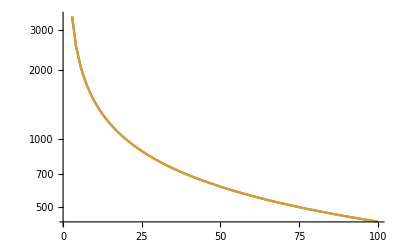

```mathematica
ND[ρofψinterp[a], {a, 2}, 6 ψtr]/d2ρAsymp[6 ψtr]
LogPlot[{ND[ρofψinterp[a], {a, 2}, ψ1 ψtr],d2ρAsymp[ψ1 ψtr]} , {ψ1, 1, 100.0}, PlotPoints->2]
```

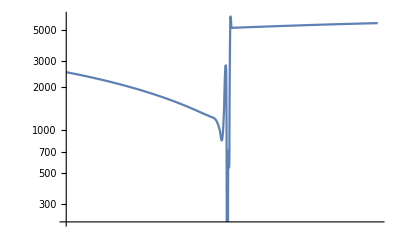

```mathematica
LogLogPlot[d2ρ[ψ1 ], {ψ1, ψtr*0.9, ψtr*1.1}]
```

Calculating the discontinuity as x = 1

```mathematica
dinner = D[ρinner[x], x]/D[ψinner[x],x]/.x->1
douter = D[ρouter[x], x]/D[ψouter[x],x]/.x->1
jump = -douter + dinner
```

54305.5

54305.5

7.27596×10^-12

```mathematica
ClearAll[f];
f[ϵ_]:=
(1/(Sqrt[8] π^2))(NIntegrate[d2ρ[ψ1]/Sqrt[ϵ - ψ1], {ψ1, 0, ϵ}]);
```

```mathematica
f[ψtr 100]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {24.548}. NIntegrate obtained 66439.6-0.000044498 ⅈ and 7.08867 for the integral and error estimates.

2380.03

```mathematica
ψ[10]
```

10.6981

```mathematica
f[0]
```

0.

```mathematica
ϵmin = 0; ϵmax = 10000;
ϵvals =Sort[N[ψtr DeleteDuplicates[Flatten[{ϵmin,10^Linspace[-2,0, 50], 10^Linspace[0, 2, 50], ϵmax}]]]]
(*ϵvals = Linspace[ψtr - 5, ψtr + 5, 50];*)
ftab = Table[{ϵ, Clip [f[ϵ], {0, 10^30}]}, {ϵ, ϵvals}];
finterp = Interpolation[ftab, InterpolationOrder->1];
```

{0.,0.24174,0.265562,0.29173,0.320478,0.352058,0.38675,0.424861,0.466727,0.512719,0.563243,0.618746,0.679717,0.746698,0.820278,0.901109,0.989905,1.08745,1.19461,1.31233,1.44165,1.58371,1.73977,1.91121,2.09954,2.30643,2.53371,2.78338,3.05766,3.35897,3.68997,4.05358,4.45302,4.89183,5.37388,5.90342,6.48515,7.12421,7.82623,8.59744,9.44464,10.3753,11.3977,12.5209,13.7547,15.1101,16.5991,18.2347,20.0316,22.0056,24.174,26.5562,29.173,32.0478,35.2058,38.675,42.4861,46.6727,51.2719,56.3243,61.8746,67.9717,74.6698,82.0278,90.1109,98.9905,108.745,119.461,131.233,144.165,158.371,173.977,191.121,209.954,230.643,253.371,278.338,305.766,335.897,368.997,405.358,445.302,489.183,537.388,590.342,648.515,712.421,782.623,859.744,944.464,1037.53,1139.77,1252.09,1375.47,1511.01,1659.91,1823.47,2003.16,2200.56,2417.4,241740.}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {1.4126542294705307922786374774659634567797183990478515625}. NIntegrate obtained 5.31321×10^-7-1.11434×10^-14 ⅈ and 9.04839×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {1.576034997600675551833460108497320106835104525089263916015625}. NIntegrate obtained 2.80553×10^-6-2.06535×10^-13 ⅈ and 1.06606×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {1.73048130986650516675851019243737027863971889019012451171875}. NIntegrate obtained 0.0000336763-4.74261×10^-14 ⅈ and 7.56663×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ftab
```

{{0.,0.},{2.4174,0.00181463},{2.53371,0.00419474},{2.65562,0.00926929},{2.78338,0.0196185},{2.9173,0.0398481},{3.05766,0.0778486},{3.20478,0.146482},{3.35897,0.265901},{3.52058,0.466572},{3.68997,0.792731},{3.8675,1.30555},{4.05358,2.0871},{4.24861,3.24417},{4.45302,4.91011},{4.66727,7.24383},{4.89183,10.4292},{5.12719,14.6736},{5.37388,20.2015},{5.63243,27.2442},{5.90342,36.0309},{6.18746,46.7851},{6.48515,59.7131},{6.79717,74.9954},{7.12421,92.7787},{7.46698,113.179},{7.82623,136.275},{8.20278,162.112},{8.59744,190.697},{9.01109,222.017},{9.44464,256.019},{9.89905,292.63},{10.3753,331.743},{10.8745,373.24},{11.3977,416.959},{11.9461,462.695},{12.5209,510.188},{13.1233,559.089},{13.7547,608.992},{14.4165,659.293},{15.1101,709.227},{15.8371,757.782},{16.5991,803.645},{17.3977,845.172},{18.2347,880.242},{19.1121,906.373},{20.0316,920.648},{20.9954,920.19},{22.0056,902.043},{23.0643,864.102},{24.174,807.661},{27.8338,1343.65},{32.0478,1637.91},{36.8997,1865.72},{42.4861,2029.38},{48.9183,2140.69},{56.3243,2214.66},{64.8515,2263.8},{74.6698,2296.88},{85.9744,2319.59},{98.9905,2335.42},{113.977,2346.75},{131.233,2354.92},{151.101,2360.51},{173.977,2364.9},{200.316,2368.45},{230.643,2370.99},{265.562,2373.26},{305.766,2374.77},{352.058,2375.93},{405.358,2376.83},{466.727,2377.54},{537.388,2378.09},{618.746,2378.53},{712.421,2378.88},{820.278,2379.15},{944.464,2379.37},{1087.45,2379.54},{1252.09,2379.68},{1441.65,2379.79},{1659.91,2379.87},{1911.21,2379.94},{2200.56,2380.},{2533.71,2380.04},{2917.3,2380.08},{3358.97,2380.11},{3867.5,2380.13},{4453.02,2380.14},{5127.19,2380.16},{5903.42,2380.17},{6797.17,2380.18},{7826.23,2380.18},{9011.09,2380.19},{10375.3,2380.19},{11946.1,2380.19},{13754.7,2380.19},{15837.1,2380.19},{18234.7,2380.2},{20995.4,2380.2},{24174.,2380.2},{241740.,2380.19}}

```mathematica
100000/ψtr
```

1331.3

```mathematica
finterp = Interpolation[ftab, InterpolationOrder->1]
```

InterpolatingFunction[{{0., 241740.}}, <>]

```mathematica
ftab
```

{{0.,0.},{0.24174,6.5016×10^-12},{0.265562,8.40151×10^-12},{0.29173,1.10552×10^-11},{0.320478,1.4828×10^-11},{0.352058,2.02918×10^-11},{0.38675,2.83564×10^-11},{0.424861,4.04951×10^-11},{0.466727,5.91342×10^-11},{0.512719,8.83379×10^-11},{0.563243,1.35025×10^-10},{0.618746,2.1115×10^-10},{0.679717,3.37623×10^-10},{0.746698,5.51289×10^-10},{0.820278,9.16961×10^-10},{0.901109,1.54649×10^-9},{0.989905,2.62284×10^-9},{1.08745,4.40917×10^-9},{1.19461,7.17718×10^-9},{1.31233,1.10489×10^-8},{1.44165,1.90332×10^-8},{1.58371,1.00501×10^-7},{1.73977,1.20637×10^-6},{1.91121,0.0000129019},{2.09954,0.000109597},{2.30643,0.000748743},{2.53371,0.00419474},{2.78338,0.0196185},{3.05766,0.0778486},{3.35897,0.265901},{3.68997,0.792731},{4.05358,2.0871},{4.45302,4.91011},{4.89183,10.4292},{5.37388,20.2015},{5.90342,36.0309},{6.48515,59.7131},{7.12421,92.7787},{7.82623,136.275},{8.59744,190.697},{9.44464,256.019},{10.3753,331.743},{11.3977,416.959},{12.5209,510.188},{13.7547,608.992},{15.1101,709.227},{16.5991,803.645},{18.2347,880.242},{20.0316,920.648},{22.0056,902.043},{24.174,807.661},{27.8338,1343.65},{32.0478,1637.91},{36.8997,1865.72},{42.4861,2029.38},{48.9183,2140.69},{56.3243,2214.66},{64.8515,2263.8},{74.6698,2296.88},{85.9744,2319.59},{98.9905,2335.42},{113.977,2346.75},{131.233,2354.92},{151.101,2360.51},{173.977,2364.9},{200.316,2368.45},{230.643,2370.99},{265.562,2373.26},{305.766,2374.77},{352.058,2375.93},{405.358,2376.83},{466.727,2377.54},{537.388,2378.09},{618.746,2378.53},{712.421,2378.88},{820.278,2379.15},{944.464,2379.37},{1087.45,2379.54},{1252.09,2379.68},{1441.65,2379.79},{1659.91,2379.87},{1911.21,2379.94},{2200.56,2380.},{2533.71,2380.04},{2917.3,2380.08},{3358.97,2380.11},{3867.5,2380.13},{4453.02,2380.14},{5127.19,2380.16},{5903.42,2380.17},{6797.17,2380.18},{7826.23,2380.18},{9011.09,2380.19},{10375.3,2380.19},{11946.1,2380.19},{13754.7,2380.19},{15837.1,2380.19},{18234.7,2380.2},{20995.4,2380.2},{24174.,2380.2},{241740.,2380.19}}

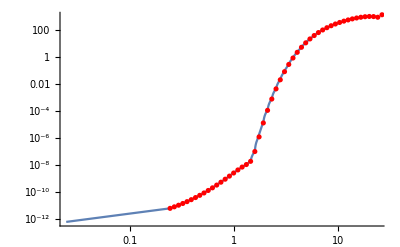

```mathematica
Show[LogLogPlot[finterp[ϵ], {ϵ, ψtr 10^-3, 1 ψtr}], ListLogLogPlot[ftab, PlotStyle->Red]]
```

```mathematica
ClearAll[vmax]
vmax[xpos_]:= Sqrt[ 2 (ψ[xpos] )];
```

```mathematica
Dens[xpos_]:= 4 π NIntegrate[v^2 finterp[ψ[xpos] - 0.5*v^2], {v, 0, vmax[xpos]}]
```

```mathematica
xpos = 10
ψ[xpos]
Dens[xpos]
ρDM[xpos]
```

10

3.44296

0.727107

0.654462

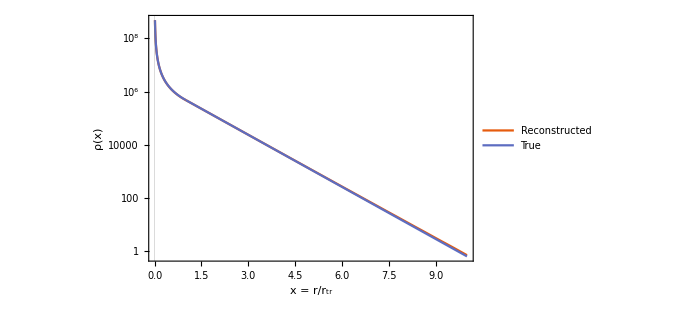

```mathematica
LogPlot[{ Dens[x], ρDM[x]}, {x, 0.01, 10}, PlotRange-> All, PlotLegends->{"Reconstructed", "True"},
 PlotTheme->"Scientific", FrameLabel->{"x = r/r_tr", "ρ(x)"}, ImageSize->500]
```

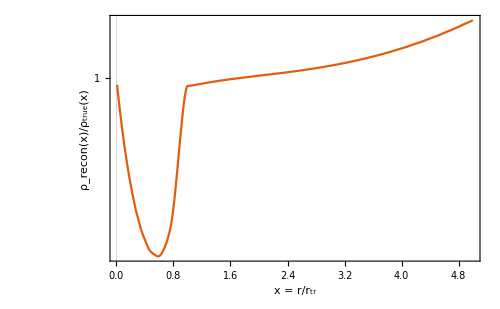

```mathematica
LogPlot[{ Dens[x]/ρDM[x]}, {x, 0.01, 5}, PlotRange-> All,
 PlotTheme->"Scientific", FrameLabel->{"x = r/r_tr", "ρ_recon(x)/ρ_true(x)"}, ImageSize->500]
```

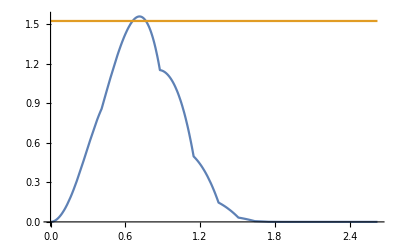

```mathematica
xpos =10;
Plot[{ 4π v^2 finterp[ψ[xpos] - 0.5*v^2]/ρDM[xpos], 4/vmax[xpos]}, {v, 0, vmax[xpos]}]
```

```mathematica
A^(1/2)
```

3784.34

```mathematica
sig[x_]:= Sqrt[ 4 π NIntegrate[v^4 finterp[ψ[x] - 0.5*v^2],{v, 0, vmax[x]}] /ρDM[x]]
```

```mathematica
N[Sqrt[3]]
N[Sqrt[4π]]
```

1.73205

3.54491

```mathematica
Print[sig[0.1]]
```

16.1183

```mathematica
Plot[ρDM[x], {x, 0.01, 5}]
```

-Graphics-

```mathematica
Plot[sig[x]/Sqrt[3], {x, 0.01, 5}, PlotRange->{0, 20}]
```

$Aborted

```mathematica
10^-3/rtr
```

0.15873

```mathematica
ftab
```

{{0.,0.},{4.04835,9.88546×10^-9},{8.0967,1.78946×10^-6},{12.1451,0.0000374461},{16.1934,0.000323927},{20.2418,0.00172692},{24.2901,0.00677846},{28.3385,0.0215393},{32.3868,0.058637},{36.4352,0.141846},{40.4835,0.312606},{44.5319,0.638914},{48.5802,1.22703},{52.6286,2.23652},{56.6769,3.89904},{60.7253,6.54156},{64.7736,10.6144},{68.822,16.7249},{72.8703,25.6768},{76.9187,38.5167},{80.967,56.5877},{85.0154,81.5909},{89.0637,115.656},{93.1121,161.419},{97.1604,222.117},{101.209,301.68},{105.257,404.853},{109.305,537.31},{113.354,705.801},{117.402,918.294},{121.451,1184.15},{125.499,1514.29},{129.547,1921.42},{133.596,2420.2},{137.644,3027.53},{141.692,3762.77},{145.741,4648.},{149.789,5708.34},{153.837,6972.27},{157.886,8471.91},{158.886,8882.73},{159.412,9105.81},{159.938,9333.72},{160.465,9566.56},{160.991,9804.42},{161.517,10047.4},{162.044,10295.5},{162.57,10549.},{163.096,10808.8},{163.623,11068.7},{163.786,11142.},{163.986,0},{164.149,0},{164.675,0},{165.202,1762.48},{165.728,2915.59},{166.254,3645.12},{166.78,4170.},{167.307,4582.45},{167.833,4896.98},{168.359,5181.7},{168.886,5415.38},{169.886,5786.37},{210.526,10620.7},{260.889,12084.3},{323.3,12591.7},{400.641,12797.3},{496.484,12896.7},{615.254,12952.2},{762.438,12982.3},{944.831,13001.2},{1170.86,13014.2},{1450.95,13020.},{1798.05,13027.9},{2228.19,13032.4},{2761.23,13029.7},{3421.78,13034.9},{4240.35,13033.2},{5254.74,13030.8},{6511.8,13040.5},{8069.57,13038.6},{10000.,13041.4}}

```mathematica
Export[NotebookDirectory[] <> "Distribution_exp.dat", ftab, "Table"]
```

/Users/bradkav/Projects/PBH_dress/PBHinDMclothing/code/Distribution_exp.dat

### Solving Eddington’s Equation - v5

Power-law cut off

```mathematica
ClearAll[A,B]
MPBH = 30;
rtr = 0.0063;
G = 4.302 10^-3;
A = 3 MPBH/(8 π rtr^3);
B = G MPBH/rtr;
γ = 8;
```

DM density profile

```mathematica
ClearAll[ρDM]
ρinner[x_]:= A x^(-3/2)
ρouter[x_]:=A x^-γ
ρDM[x_]:= Piecewise[{{ρinner[x], x < 1},{ρouter[x], x≥ 1}}]
```

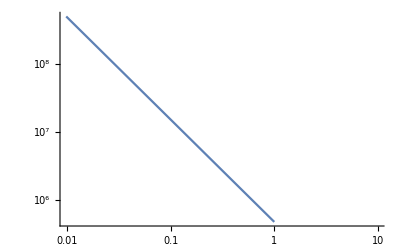

```mathematica
LogLogPlot[ρDM[x], {x, 0, 10}]
```

Potentials

```mathematica
Integrate[Minner[x]/x^2, {x, 1, x1}]
```

ConditionalExpression[-30+(30 (-1+2 x1^(3/2)))/x1,Re[x1]>0||x1∉Reals]

```mathematica
ClearAll[ ψ, Minner, Mouter,Menc, ψouter, ψinner]
Minner[x_]:=MPBH (1+x^(3/2));
Mouter[x_]=2MPBH + 3/(2(γ - 3))MPBH (1- x^(3-γ));
Menc[x_] :=  Piecewise[{{Mouter[x], x >= 1},{Minner[x], x < 1}}]
ψouter[x_]= G Assuming[ x > 1, rtr^-3 Integrate[Mouter[x1]/x1^2, {x1, x, ∞}]];
ψinner[x_] = ψouter[1] + B(1 + x^-1 - 2 x^(1/2));
ψ[x_] := Piecewise[{{ψouter[x],x ≥1},{ψinner[x],x < 1}}]
ψtr = ψ[1];
ρtr = ρDM[1];
```

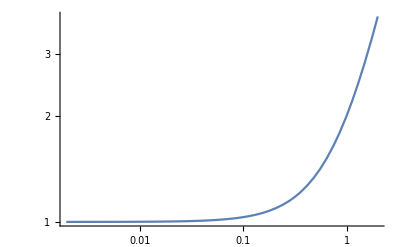

```mathematica
LogLogPlot[Menc[x]/MPBH, {x, 0, 2}, PlotRange->All]
```

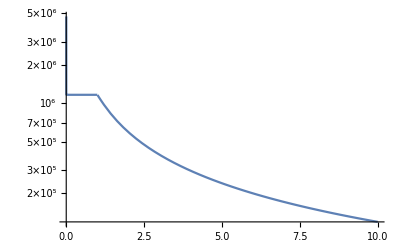

```mathematica
LogPlot[ψ[x], {x, 0, 10}]
```

Inverting the potentials

```mathematica
ψinvOuter[ψ1_]= x/.Assuming[1 ≤ x && 0 ≤ ψ1 ≤ ψtr && B > 0 && ψ1 ∈ Reals && B ∈ Reals ,
Simplify[Solve[ψouter[x] == ψ1 ,x,Reals][[2]]]]
ψinvInner[ψ1_]=x/.Assuming[ψ1 ≥ 0 && B > 0 && ψ1 ∈ Reals && B ∈ Reals ,
Simplify[Solve[ψinner[x] == ψ1 ,x,Reals][[1]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Root[3.10775×10^17-1.42957×10^19 #1^5+1.20422×10^13 ψ1 #1^6&,2]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Root[-1.4206×10^17+(-1.61068×10^22+1.38692×10^16 ψ1) #1+(-4.56551×10^26+7.86247×10^20 ψ1-3.38508×10^14 ψ1^2) #1^2+5.68239×10^17 #1^3&,1]

```mathematica
ψinvOuter[100000]
```

11.8713

```mathematica
ψinv[ψ1_]:= Piecewise[{{ψinvOuter[ψ1], ψ1 < ψtr},{ψinvInner[ψ1], ψ1 ≥ ψtr}}]
```

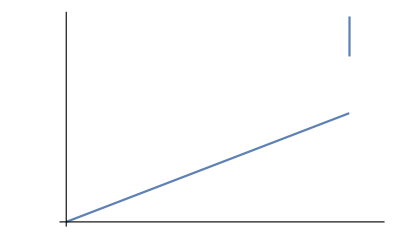

```mathematica
ρofψ[ψ1_]:= ρDM[ψinv[ψ1]]
LogLogPlot[ρofψ[ψ1], {ψ1, ψtr - 1000, ψtr + 100}]
```

Asymptotic derivatives

```mathematica
ClearAll[dρAsymp, d2ρAsymp]
dρAsymp[ψ1_]:= (3/2)A (ψ1 - ( ψouter[1] + B))^(1/2)/B^(3/2)
d2ρAsymp[ψ1_]:= (3/4)A (ψ1-( ψouter[1] + B))^(-1/2)/B^(3/2)
```

```mathematica
ClearAll[d2ρ]
d2ρ[ψ1]:= Piecewise[{
{ND[ρofψ[a], {a, 2}, ψtr - 0.5], ψtr - 0.5< ψ1 ≤ ψtr},
{ND[ρofψ[a], {a, 2}, ψtr + 0.5], ψtr < ψ1 ≤ ψtr+0.5},
{ND[ρofψ[a], {a, 2}, ψ1], ψ1 < 1000},
{d2ρAsymp[ψ1], ψ1 ≥1000}}
]
```

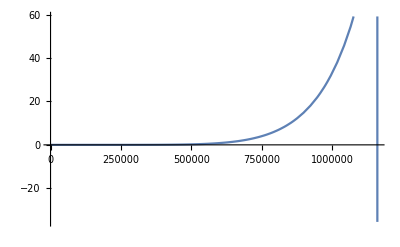

```mathematica
Plot[ND[ρofψ[a], {a, 1}, ψ1], {ψ1, 0, 1 ψtr}]
```

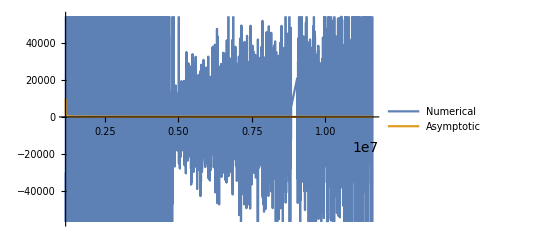

```mathematica
Plot[{ND[ρofψ[a], {a, 2}, ψ1], d2ρAsymp[ψ1]}, {ψ1, ψtr,  10ψtr}, PlotLegends->{"Numerical", "Asymptotic"}]
```

Calculating the discontinuity as x = 1

```mathematica
dinner = D[ρinner[x], x]/D[ψinner[x],x]/.x->1
douter = D[ρouter[x], x]/D[ψouter[x],x]/.x->1
jump = -douter + dinner
```

524314.

110.987

524203.

```mathematica
f[ϵ_]:=If[ϵ < ψtr, 
(1/(Sqrt[8] π^2))(NIntegrate[d2ρ[ψ1]/Sqrt[ϵ - ψ1], {ψ1, 0, ϵ}]),
(1/(Sqrt[8] π^2))(NIntegrate[d2ρ[ψ1]/Sqrt[ϵ - ψ1], {ψ1, 0,ϵ}]  + jump/Sqrt[ϵ - ψtr])];
```

```mathematica
f[0]
```

0.

```mathematica
ϵmin = 0; ϵmax = 2000;
ϵvals = Sort[N[Flatten[{ Linspace[ψtr - 5, ψtr + 5,20],Linspace[0, ψtr-6, 40], ψtr-0.1, ψtr + 0.1, 10^Linspace[Log10[ψtr+6], Log10[10000], 20]}]]]
(*ϵvals = Linspace[ψtr - 5, ψtr + 5, 50];*)
ftab = Table[{ϵ, Clip [f[ϵ], {0, 10^30}]}, {ϵ, ϵvals}];
finterp = Interpolation[ftab, InterpolationOrder->1];
Plot[finterp[ϵ], {ϵ, ϵmin, ϵmax}, GridLines->{{ ψtr},{}}]
```

{1.16132×10^6,1.16132×10^6,10.^Linspace[6.06495,4.,20.],Linspace[0.,1.16132×10^6,40.],Linspace[1.16132×10^6,1.16133×10^6,20.]}

NIntegrate::inumr: The integrand ({ | «1»)/(√(1.16132×10^6-ψ1)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,66.1868}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand ({ | «1»)/(√(1.16132×10^6-ψ1)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,66.1868}}.

Interpolation::indat: Data point {10.^Linspace[6.06495,4.,20.],Clip[If[10.^Linspace[6.06495,4.,20.]<1.16132×10^6,NIntegrate[d2ρ[ψ1]/(√(«1»)),{ψ1,0,(«4»)^(«1»)}]/(√(«1») Power[«2»]),(NIntegrate[d2ρ[«1»] Power[«2»],{ψ1,0,Power[«2»]}]+jump/(√(«1»)))/(√(«1») Power[«2»])],{0,1000000000000000000000000000000}]} contains abscissa 10.^Linspace[6.06495,4.,20.], which is not a real number.

NIntegrate::inumr: The integrand ({ | «1»)/(√(1.16132×10^6-ψ1)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,66.1868}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Interpolation::indat: Data point {10.^Linspace[6.06495,4.,20.],Clip[If[10.^Linspace[6.06495,4.,20.]<1.16132×10^6,NIntegrate[d2ρ[ψ1]/(√(«1»)),{ψ1,0,(«4»)^(«1»)}]/(√(«1») Power[«2»]),(NIntegrate[d2ρ[«1»] Power[«2»],{ψ1,0,Power[«2»]}]+jump/(√(«1»)))/(√(«1») Power[«2»])],{0,1000000000000000000000000000000}]} contains abscissa 10.^Linspace[6.06495,4.,20.], which is not a real number.

$Aborted[]

NIntegrate::inumr: The integrand ({ | «1»)/(√(1.16132×10^6-ψ1)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,66.1868}}.

Interpolation::indat: Data point {10.^Linspace[6.06495,4.,20.],Clip[If[10.^Linspace[6.06495,4.,20.]<1.16132×10^6,NIntegrate[d2ρ[ψ1]/(√(«1»)),{ψ1,0,(«4»)^(«1»)}]/(√(«1») Power[«2»]),(NIntegrate[d2ρ[«1»] Power[«2»],{ψ1,0,Power[«2»]}]+jump/(√(«1»)))/(√(«1») Power[«2»])],{0,1000000000000000000000000000000}]} contains abscissa 10.^Linspace[6.06495,4.,20.], which is not a real number.

NIntegrate::inumr: The integrand ({ | «1»)/(√(1.16132×10^6-1. ψ1)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,66.1868}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
Log10[ftab]
```

{{-5.,-20.0338},{0.607279,-8.005},{0.908309,-5.74727},{1.0844,-4.42659},{1.20934,-3.48955},{1.30625,-2.76273},{1.38543,-2.16887},{1.45238,-1.66677},{1.51037,-1.23183},{1.56152,-0.848184},{1.60728,-0.505002},{1.64867,-0.194557},{1.68646,0.0888568},{1.72122,0.349573},{1.75341,0.590958},{1.78337,0.815682},{1.8114,1.0259},{1.83773,1.22336},{1.86255,1.40954},{1.88603,1.58565},{1.90831,1.75272},{1.9295,1.91164},{1.9497,2.06317},{1.96901,2.20796},{1.98749,2.34658},{2.00522,2.47955},{2.02225,2.6073},{2.03864,2.73023},{2.05444,2.84868},{2.06968,2.96298},{2.0844,3.07341},{2.09864,3.18021},{2.11243,3.28362},{2.12579,3.38385},{2.13876,3.48109},{2.15135,3.57551},{2.16358,3.66727},{2.17548,3.75651},{2.18706,3.84337},{2.19834,3.92798},{2.20108,3.94855},{2.20252,3.95932},{2.20395,3.97005},{2.20538,3.98076},{2.2068,3.99142},{2.20822,4.00205},{2.20963,4.01265},{2.21104,4.02321},{2.21244,4.03378},{2.21384,4.0441},{2.21428,4.04696},{2.21481,4.27795+1.36438 ⅈ},{2.21524,3.89206+1.36438 ⅈ},{2.21663,2.63033+1.36438 ⅈ},{2.21801,3.24612},{2.2194,3.46473},{2.22077,3.56171},{2.22215,3.62014},{2.22351,3.6611},{2.22488,3.68993},{2.22624,3.71447},{2.22759,3.73363},{2.23016,3.76241},{2.32331,4.02615},{2.41646,4.08222},{2.50961,4.10009},{2.60276,4.10712},{2.69591,4.11048},{2.78905,4.11235},{2.8822,4.11335},{2.97535,4.11398},{3.0685,4.11442},{3.16165,4.11461},{3.2548,4.11487},{3.34795,4.11502},{3.4411,4.11493},{3.53425,4.11511},{3.6274,4.11505},{3.72055,4.11497},{3.8137,4.11529},{3.90685,4.11523},{4.,4.11532}}

```mathematica
ϵvals
```

{0.00001,4.04836,8.09671,12.1451,16.1934,20.2418,24.2901,28.3385,32.3868,36.4352,40.4835,44.5319,48.5802,52.6286,56.6769,60.7253,64.7736,68.822,72.8703,76.9187,80.967,85.0154,89.0637,93.1121,97.1604,101.209,105.257,109.305,113.354,117.402,121.451,125.499,129.547,133.596,137.644,141.692,145.741,149.789,153.837,157.886,158.886,159.412,159.938,160.465,160.991,161.517,162.044,162.57,163.096,163.623,163.786,163.986,164.149,164.675,165.202,165.728,166.254,166.78,167.307,167.833,168.359,168.886,169.886,210.526,260.889,323.3,400.641,496.484,615.254,762.438,944.831,1170.86,1450.95,1798.05,2228.19,2761.23,3421.78,4240.35,5254.74,6511.8,8069.57,10000.}

```mathematica
Show[LogLogPlot[finterp[ϵ], {ϵ, 50, 500}], ListLogLogPlot[ftab, PlotStyle->Red]]
```

-Graphics-

```mathematica
ClearAll[vmax]
vmax[xpos_]:= Sqrt[ 2 (ψ[xpos] )];
```

```mathematica
Dens[xpos_]:= 4 π NIntegrate[v^2 finterp[ψ[xpos] - 0.5*v^2], {v, 0, vmax[xpos]}]
```

```mathematica
xpos = 10.0
ψ[xpos]
Dens[xpos]
ρDM[xpos]
```

10.

92.1597

81473.8

80534.3

```mathematica
LogPlot[{ Dens[x], ρDM[x]}, {x, 0.01, 5}, PlotRange-> All, PlotLegends->{"Reconstructed", "True"},
 PlotTheme->"Scientific", FrameLabel->{"x = r/r_tr", "ρ(x)"}, ImageSize->500]
```

$Aborted

```mathematica
LogPlot[{ Dens[x]/ρDM[x]}, {x, 0.01, 5}, PlotRange-> All,
 PlotTheme->"Scientific", FrameLabel->{"x = r/r_tr", "ρ_recon(x)/ρ_true(x)"}, ImageSize->500]
```

-Graphics-

```mathematica
xpos =0.9;
Plot[{ 4π v^2 finterp[ψ[xpos] - 0.5*v^2]/ρDM[xpos]}, {v, 0, vmax[xpos]}]
```

-Graphics-

```mathematica
A^(1/2)
```

3784.34

```mathematica
sig[x_]:= Sqrt[ 4 π NIntegrate[v^4 finterp[ψ[x] - 0.5*v^2],{v, 0, vmax[x]}] /ρDM[x]]
```

```mathematica
N[Sqrt[3]]
N[Sqrt[4π]]
```

1.73205

3.54491

```mathematica
Print[sig[0.1]]
```

16.1183

```mathematica
Plot[ρDM[x], {x, 0.01, 5}]
```

-Graphics-

```mathematica
Plot[sig[x]/Sqrt[3], {x, 0.01, 5}, PlotRange->{0, 20}]
```

$Aborted

```mathematica
ftab
```

{{0.,0.},{4.04835,9.88546×10^-9},{8.0967,1.78946×10^-6},{12.1451,0.0000374461},{16.1934,0.000323927},{20.2418,0.00172692},{24.2901,0.00677846},{28.3385,0.0215393},{32.3868,0.058637},{36.4352,0.141846},{40.4835,0.312606},{44.5319,0.638914},{48.5802,1.22703},{52.6286,2.23652},{56.6769,3.89904},{60.7253,6.54156},{64.7736,10.6144},{68.822,16.7249},{72.8703,25.6768},{76.9187,38.5167},{80.967,56.5877},{85.0154,81.5909},{89.0637,115.656},{93.1121,161.419},{97.1604,222.117},{101.209,301.68},{105.257,404.853},{109.305,537.31},{113.354,705.801},{117.402,918.294},{121.451,1184.15},{125.499,1514.29},{129.547,1921.42},{133.596,2420.2},{137.644,3027.53},{141.692,3762.77},{145.741,4648.},{149.789,5708.34},{153.837,6972.27},{157.886,8471.91},{158.886,8882.73},{159.412,9105.81},{159.938,9333.72},{160.465,9566.56},{160.991,9804.42},{161.517,10047.4},{162.044,10295.5},{162.57,10549.},{163.096,10808.8},{163.623,11068.7},{163.786,11142.},{163.986,0},{164.149,0},{164.675,0},{165.202,1762.48},{165.728,2915.59},{166.254,3645.12},{166.78,4170.},{167.307,4582.45},{167.833,4896.98},{168.359,5181.7},{168.886,5415.38},{169.886,5786.37},{210.526,10620.7},{260.889,12084.3},{323.3,12591.7},{400.641,12797.3},{496.484,12896.7},{615.254,12952.2},{762.438,12982.3},{944.831,13001.2},{1170.86,13014.2},{1450.95,13020.},{1798.05,13027.9},{2228.19,13032.4},{2761.23,13029.7},{3421.78,13034.9},{4240.35,13033.2},{5254.74,13030.8},{6511.8,13040.5},{8069.57,13038.6},{10000.,13041.4}}

```mathematica
Export[NotebookDirectory[] <> "Distribution.dat", ftab, "Table"]
```

/Users/bradkav/Projects/PBH_dress/PBHinDMclothing/code/Distribution.dat

$Aborted

### Solving Eddington’s Equation - v6

Hard truncation

```mathematica
ClearAll[A,B]
MPBH = 30;
rtr = 0.0063*(MPBH^(1/3));
G = 4.302 10^-3;
A = 3 MPBH/(8 π rtr^3);
B = G MPBH/rtr;
```

DM density profile

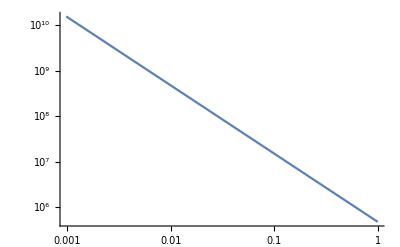

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 4702178790116439-9404357580232877 Log[ⅇ^(1/β)] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

787058.

2.

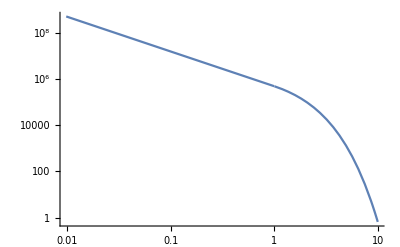

```mathematica
ClearAll[ρDM, α, β]
ρDM[x_]:= A x^(-3/2)
LogLogPlot[ρDM[x], {x, 0, 1}]
```

Potentials

```mathematica
ClearAll[ ψ, Minner, Mouter,Menc, ψouter, ψinner]
Minner[x_]:=MPBH (1+x^(3/2));
Menc[x_] :=  Minner[x]
ψinner[x_] := B(1 + x^-1 - 2 x^(1/2));
ψ[x_] := ψinner[x]
ψtr = ψ[1];
ρtr = ρDM[1];
```

```mathematica
ψ[0.6]
```

7.3674

```mathematica
ψouter[x]
```

13.1858/x

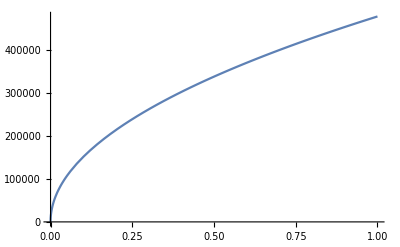

```mathematica
Plot[ρDM[x]x^2, {x, 0, 1}]
```

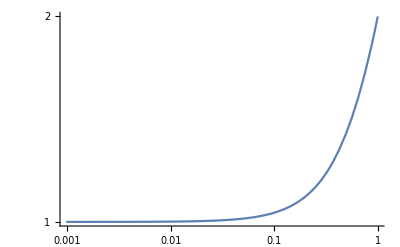

```mathematica
LogLogPlot[Menc[x]/MPBH, {x, 0, 1}, PlotRange->All]
```

```mathematica
ψmax = ψ[10^-5]
```

659298.

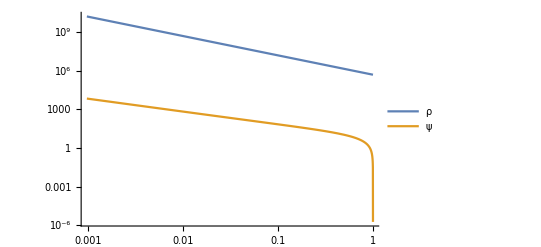

```mathematica
LogLogPlot[{ρDM[x],ψ[x]}, {x, 0, 1}, PlotLegends->{"ρ", "ψ"}]
```

Inverting the potentials

```mathematica
ψinv[ψ1_]=x/.Assuming[ ψ1 ≥ 0 && B > 0 && ψ1 ∈ Reals && B ∈ Reals ,
Simplify[Solve[ψ[x] == ψ1 ,x,Reals]]]
```

```mathematica
ψinv[10.5]
```

{0.498741}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ψtr
```

0.

```mathematica
l  = ψinvOuter[ψtr - 10]
```

{4.1389}

```mathematica
l[[3]]
```

26.9541

```mathematica
ρofψ[ψ1_]:= If[ψ1 == 0, 0, ρDM[ψinv[ψ1][[1]]]]
```

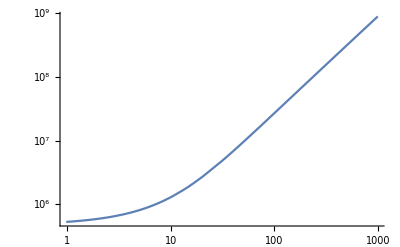

```mathematica
LogLogPlot[ρofψ[ψ1], {ψ1, 0, 1000}, PlotPoints->2]
```

```mathematica
ρofψ[15]
```

1.92339×10^6

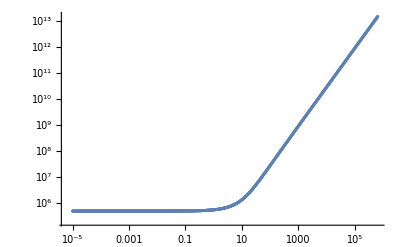

```mathematica
ψvals = DeleteDuplicates[Flatten[{0,10^Linspace[-5, Log10[ψmax], 1000]}]];
ρtab = Table[{ψ1,ρofψ[ψ1]}, {ψ1,ψvals}];
ListLogLogPlot[ρtab]
```

```mathematica
ρofψinterp = Interpolation[ρtab];
```

```mathematica
ρofψ[1]
```

534289.

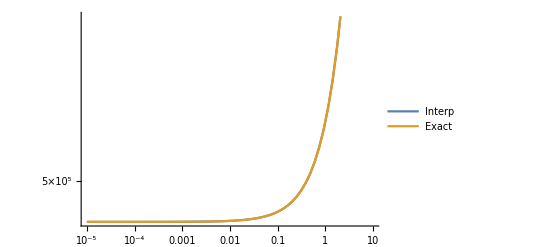

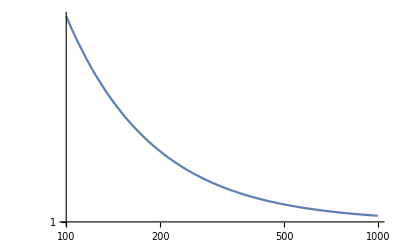

```mathematica
LogLogPlot[{ρofψinterp[ψ1], ρofψ[ψ1]}, {ψ1, 10^-5, 10}, PlotPoints->2, PlotLegends->{"Interp", "Exact", "Asymptotic"}]
LogLogPlot[{ρofψinterp[ψ1]/ρAsymp[ψ1]}, {ψ1, 100, 1000}, PlotPoints->2]
```

Asymptotic derivatives

```mathematica
ClearAll[dρAsymp, d2ρAsymp]
ρAsymp[ψ1_] := A(ψ1/B - 1)^(3/2)
dρAsymp[ψ1_]:= (3/2)A (ψ1 - B)^(1/2)/B^(3/2)
d2ρAsymp[ψ1_]:= (3/4)A (ψ1-B)^(-1/2)/B^(3/2)
```

```mathematica
ClearAll[d2ρ]
d2ρ[ψ1]:= Piecewise[{
{ND[ρofψinterp[a], {a, 2}, ψ1], ψ1 < 1000},
{d2ρAsymp[ψ1], ψ1 ≥1000}}
]
```

```mathematica
ψ[0.999]
```

0.0131941

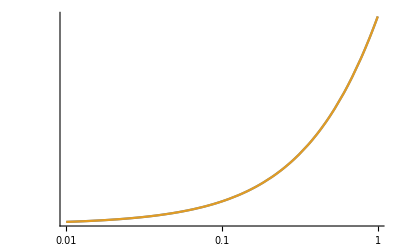

```mathematica
LogLogPlot[{ND[ρofψinterp[a], {a, 2}, ψ1 ], d2ρ[ψ1]} , {ψ1, 10^-2, 10^-0}, PlotPoints->10]
```

```mathematica
ND[ρofψinterp[a], {a, 2}, 6 ψtr]/d2ρAsymp[6 ψtr]
LogPlot[{ND[ρofψinterp[a], {a, 2}, ψ1 ψtr],d2ρAsymp[ψ1 ψtr]} , {ψ1, 1, 100.0}, PlotPoints->2]
```

0.998723

Power::infy: Infinite expression 1/(√0.) encountered.

-Graphics-

```mathematica
LogLogPlot[d2ρ[ψ1 ], {ψ1, ψtr*0.9, ψtr*1.1}]
```

Plot::plld: Endpoints for ψ1 in {ψ1,0.,0.} must have distinct machine-precision numerical values.

LogLogPlot[d2ρ[ψ1],{ψ1,ψtr 0.9,ψtr 1.1}]

Calculating the discontinuity as x = 1

```mathematica
dinner = D[ρinner[x], x]/D[ψinner[x],x]/.x->1
douter = D[ρouter[x], x]/D[ψouter[x],x]/.x->1
jump = -douter + dinner
```

54305.5

54305.5

7.27596×10^-12

```mathematica
ClearAll[f];
f[ϵ_]:=
(1/(Sqrt[8] π^2))(Re[NIntegrate[d2ρ[ψ1]/Sqrt[ϵ - ψ1], {ψ1, 0, ϵ}]] + ϵ^(-1/2) (3A)/(4B));
```

```mathematica
NIntegrate[d2ρ[ψ1]/Sqrt[0.002 - ψ1], {ψ1, 0, 0.002}]
```

-294919.-0.0000124997 ⅈ

```mathematica
f[0.002]
```

76434.2

```mathematica
d2ρ[0.002]
```

d2ρ[0.002]

```mathematica
ψ[10]
```

-34.445

```mathematica
ρofψ[10^-5]
```

477376.

```mathematica
f[0]
```

0.

```mathematica
f[10^-4]
```

146745.

```mathematica
ψ[0.99999]
```

0.000131859

```mathematica
ϵmin = 0; ϵmax = ψmax;
ϵvals =N[DeleteDuplicates[Flatten[{10^Linspace[-10,-1,100],10^Linspace[-1,1,50],10^Linspace[1,3,30], 10000, ψmax}]]]
(*ϵvals = N[Flatten[10^Linspace[-5,0,50]]]*)
ftab = Table[{ϵ, Clip [f[ϵ], {0, 10^30}]}, {ϵ, ϵvals}];
finterp = Interpolation[ftab, InterpolationOrder->1];
```

{1.×10^-10,1.23285×10^-10,1.51991×10^-10,1.87382×10^-10,2.31013×10^-10,2.84804×10^-10,3.51119×10^-10,4.32876×10^-10,5.3367×10^-10,6.57933×10^-10,8.11131×10^-10,1.×10^-9,1.23285×10^-9,1.51991×10^-9,1.87382×10^-9,2.31013×10^-9,2.84804×10^-9,3.51119×10^-9,4.32876×10^-9,5.3367×10^-9,6.57933×10^-9,8.11131×10^-9,1.×10^-8,1.23285×10^-8,1.51991×10^-8,1.87382×10^-8,2.31013×10^-8,2.84804×10^-8,3.51119×10^-8,4.32876×10^-8,5.3367×10^-8,6.57933×10^-8,8.11131×10^-8,1.×10^-7,1.23285×10^-7,1.51991×10^-7,1.87382×10^-7,2.31013×10^-7,2.84804×10^-7,3.51119×10^-7,4.32876×10^-7,5.3367×10^-7,6.57933×10^-7,8.11131×10^-7,1.×10^-6,1.23285×10^-6,1.51991×10^-6,1.87382×10^-6,2.31013×10^-6,2.84804×10^-6,3.51119×10^-6,4.32876×10^-6,5.3367×10^-6,6.57933×10^-6,8.11131×10^-6,0.00001,0.0000123285,0.0000151991,0.0000187382,0.0000231013,0.0000284804,0.0000351119,0.0000432876,0.000053367,0.0000657933,0.0000811131,0.0001,0.000123285,0.000151991,0.000187382,0.000231013,0.000284804,0.000351119,0.000432876,0.00053367,0.000657933,0.000811131,0.001,0.00123285,0.00151991,0.00187382,0.00231013,0.00284804,0.00351119,0.00432876,0.0053367,0.00657933,0.00811131,0.01,0.0123285,0.0151991,0.0187382,0.0231013,0.0284804,0.0351119,0.0432876,0.053367,0.0657933,0.0811131,0.1,0.109854,0.120679,0.132571,0.145635,0.159986,0.175751,0.19307,0.212095,0.232995,0.255955,0.281177,0.308884,0.339322,0.372759,0.409492,0.449843,0.494171,0.542868,0.596362,0.655129,0.719686,0.790604,0.868511,0.954095,1.04811,1.1514,1.26486,1.3895,1.52642,1.67683,1.84207,2.02359,2.223,2.44205,2.6827,2.94705,3.23746,3.55648,3.90694,4.29193,4.71487,5.17947,5.68987,6.25055,6.86649,7.54312,8.28643,9.10298,10.,11.721,13.7382,16.1026,18.8739,22.1222,25.9294,30.392,35.6225,41.7532,48.939,57.3615,67.2336,78.8046,92.3671,108.264,126.896,148.735,174.333,204.336,239.503,280.722,329.034,385.662,452.035,529.832,621.017,727.895,853.168,1000.,10000.,659298.}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {8.37389}. NIntegrate obtained 34441.-4.00127×10^-6 ⅈ and 0.038814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {9.4808374310595671108359283607569523155689239501953125}. NIntegrate obtained 36040.6 and 0.0560498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {10.5075}. NIntegrate obtained 38768.6-3.9001×10^-6 ⅈ and 0.0578547 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
ftab
```

{{0.00001,443391.},{0.0000162378,356449.},{0.0000263665,282762.},{0.0000428133,223186.},{0.0000695193,175726.},{0.000112884,138173.},{0.000183298,108561.},{0.000297635,85256.8},{0.000483293,66938.1},{0.00078476,52548.2},{0.00127427,41249.4},{0.00206914,32380.6},{0.00335982,25420.7},{0.00545559,19960.4},{0.00885867,15677.8},{0.0143845,12320.5},{0.0233572,9690.41},{0.0379269,7632.33},{0.0615848,6024.82},{0.1,4773.05},{0.109854,4564.98},{0.120679,4366.99},{0.132571,4178.66},{0.145635,3999.56},{0.159986,3829.31},{0.175751,3667.53},{0.19307,3513.85},{0.212095,3367.96},{0.232995,3229.52},{0.255955,3098.23},{0.281177,2973.81},{0.308884,2855.98},{0.339322,2744.48},{0.372759,2639.09},{0.409492,2539.55},{0.449843,2445.68},{0.494171,2357.25},{0.542868,2274.08},{0.596362,2196.01},{0.655129,2707.19},{0.719686,2611.99},{0.790604,2522.65},{0.868511,2438.99},{0.954095,2360.84},{1.04811,2288.04},{1.1514,2220.44},{1.26486,2157.92},{1.3895,2100.36},{1.52642,2047.66},{1.67683,1999.71},{1.84207,1956.45},{2.02359,1917.79},{2.223,1883.67},{2.44205,1854.04},{2.6827,1828.87},{2.94705,1808.1},{3.23746,1791.69},{3.55648,1779.62},{3.90694,1771.84},{4.29193,1768.3},{4.71487,1768.93},{5.17947,1773.64},{5.68987,1782.33},{6.25055,1794.84},{6.86649,1811.},{7.54312,1830.53},{8.28643,1853.16},{9.10298,1878.53},{10.,1906.24},{11.721,1957.},{13.7382,2010.59},{16.1026,2064.4},{18.8739,2115.99},{22.1222,2163.4},{25.9294,2205.33},{30.392,2241.17},{35.6225,2271.09},{41.7532,2295.03},{48.939,2314.3},{57.3615,2329.34},{67.2336,2341.06},{78.8046,2350.1},{92.3671,2356.98},{108.264,2362.38},{126.896,2366.45},{148.735,2330.17},{174.333,2336.42},{204.336,2340.73},{239.503,2375.32},{280.722,2376.44},{329.034,2351.21},{385.662,2353.89},{452.035,2378.49},{529.832,2378.88},{621.017,2360.23},{727.895,2361.96},{853.168,2363.43},{1000.,2364.88},{10000.,2375.48},{659298.,2379.6}}

```mathematica
100000/ψtr
```

1331.3

```mathematica
finterp = Interpolation[ftab, InterpolationOrder->1]
```

-10
InterpolatingFunction[{{1. 10   , 659298.}}, <>]

```mathematica
ftab
```

{{0.00001,443391.},{0.0000162378,356449.},{0.0000263665,282762.},{0.0000428133,223186.},{0.0000695193,175726.},{0.000112884,138173.},{0.000183298,108561.},{0.000297635,85256.8},{0.000483293,66938.1},{0.00078476,52548.2},{0.00127427,41249.4},{0.00206914,32380.6},{0.00335982,25420.7},{0.00545559,19960.4},{0.00885867,15677.8},{0.0143845,12320.5},{0.0233572,9690.41},{0.0379269,7632.33},{0.0615848,6024.82},{0.1,4773.05},{0.109854,4564.98},{0.120679,4366.99},{0.132571,4178.66},{0.145635,3999.56},{0.159986,3829.31},{0.175751,3667.53},{0.19307,3513.85},{0.212095,3367.96},{0.232995,3229.52},{0.255955,3098.23},{0.281177,2973.81},{0.308884,2855.98},{0.339322,2744.48},{0.372759,2639.09},{0.409492,2539.55},{0.449843,2445.68},{0.494171,2357.25},{0.542868,2274.08},{0.596362,2196.01},{0.655129,2707.19},{0.719686,2611.99},{0.790604,2522.65},{0.868511,2438.99},{0.954095,2360.84},{1.04811,2288.04},{1.1514,2220.44},{1.26486,2157.92},{1.3895,2100.36},{1.52642,2047.66},{1.67683,1999.71},{1.84207,1956.45},{2.02359,1917.79},{2.223,1883.67},{2.44205,1854.04},{2.6827,1828.87},{2.94705,1808.1},{3.23746,1791.69},{3.55648,1779.62},{3.90694,1771.84},{4.29193,1768.3},{4.71487,1768.93},{5.17947,1773.64},{5.68987,1782.33},{6.25055,1794.84},{6.86649,1811.},{7.54312,1830.53},{8.28643,1853.16},{9.10298,1878.53},{10.,1906.24},{11.721,1957.},{13.7382,2010.59},{16.1026,2064.4},{18.8739,2115.99},{22.1222,2163.4},{25.9294,2205.33},{30.392,2241.17},{35.6225,2271.09},{41.7532,2295.03},{48.939,2314.3},{57.3615,2329.34},{67.2336,2341.06},{78.8046,2350.1},{92.3671,2356.98},{108.264,2362.38},{126.896,2366.45},{148.735,2330.17},{174.333,2336.42},{204.336,2340.73},{239.503,2375.32},{280.722,2376.44},{329.034,2351.21},{385.662,2353.89},{452.035,2378.49},{529.832,2378.88},{621.017,2360.23},{727.895,2361.96},{853.168,2363.43},{1000.,2364.88},{10000.,2375.48},{659298.,2379.6}}

```mathematica
finterp[10000]
finterp[ψmax]
```

2375.48

2379.6

```mathematica
ψ[0.95]
```

0.680868

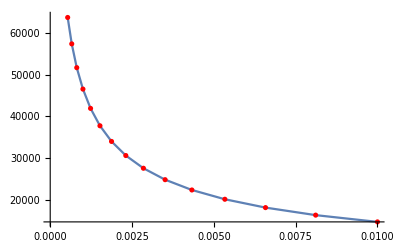

```mathematica
Show[Plot[finterp[ϵ], {ϵ, 10^-5, 10^-2}], ListPlot[ftab, PlotStyle->Red]]
```

```mathematica
ClearAll[vmax]
vmax[xpos_]:= Sqrt[ 2 (ψ[xpos] )];
```

```mathematica
ψ[0.99]
```

0.13269

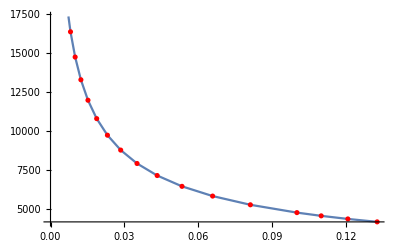

```mathematica
Show[Plot[finterp[ϵ], {ϵ, 10^-5, ψ[0.99]}], ListPlot[ftab, PlotStyle->Red]]
```

```mathematica
Dens[xpos_]:= 4 π NIntegrate[v^2 finterp[ψ[xpos] - 0.5*v^2], {v, 0, vmax[xpos]}]
```

```mathematica
xpos = 0.99;
ψ[xpos]
Dens[xpos]
ρDM[xpos]
```

0.13269

5513.46

484626.

```mathematica
0.5
```

0.13269

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

484626.

```mathematica
Dens[xpos]/ρDM[xpos]
```

0.0113269

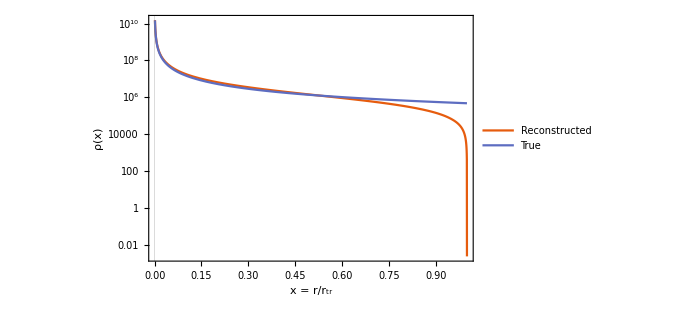

```mathematica
LogPlot[{ Dens[x], ρDM[x]}, {x, 0.001, 1}, PlotRange-> All, PlotLegends->{"Reconstructed", "True"},
 PlotTheme->"Scientific", FrameLabel->{"x = r/r_tr", "ρ(x)"}, ImageSize->500]
```

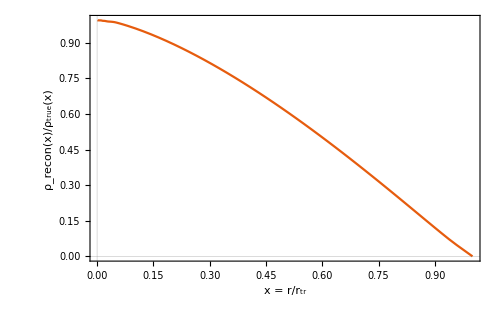

```mathematica
Plot[{ Dens[x]/ρDM[x]}, {x, 0.001, 1}, PlotRange-> All,
 PlotTheme->"Scientific", FrameLabel->{"x = r/r_tr", "ρ_recon(x)/ρ_true(x)"}, ImageSize->500]
```

```mathematica
ρtab = Table[{x, Dens[x]/ρDM[x]}, {x, N[10^Linspace[-5, 0, 100]]}]
```

{{0.00001,0.998648},{0.0000112332,0.998564},{0.0000126186,0.998488},{0.0000141747,0.998419},{0.0000159228,0.998355},{0.0000178865,0.998296},{0.0000200923,0.998241},{0.0000225702,0.99819},{0.0000253536,0.998141},{0.0000284804,0.998094},{0.0000319927,0.998049},{0.0000359381,0.998004},{0.0000403702,0.997959},{0.0000453488,0.997914},{0.0000509414,0.997868},{0.0000572237,0.99782},{0.0000642807,0.997771},{0.0000722081,0.997718},{0.0000811131,0.997662},{0.0000911163,0.997601},{0.000102353,0.997536},{0.000114976,0.997465},{0.000129155,0.997388},{0.000145083,0.997303},{0.000162975,0.99721},{0.000183074,0.997108},{0.000205651,0.996996},{0.000231013,0.996874},{0.000259502,0.996739},{0.000291505,0.996592},{0.000327455,0.996431},{0.000367838,0.996256},{0.000413201,0.996068},{0.000464159,0.995866},{0.000521401,0.995653},{0.000585702,0.995431},{0.000657933,0.99521},{0.000739072,0.995007},{0.000830218,0.99483},{0.000932603,0.994675},{0.00104762,0.99454},{0.00117681,0.994424},{0.00132194,0.994323},{0.00148497,0.994238},{0.0016681,0.994165},{0.00187382,0.994105},{0.0021049,0.994054},{0.00236449,0.994012},{0.00265609,0.993977},{0.00298365,0.993949},{0.0033516,0.993925},{0.00376494,0.993904},{0.00422924,0.993884},{0.00475081,0.993864},{0.0053367,0.993841},{0.00599484,0.993813},{0.00673415,0.993782},{0.00756463,0.993749},{0.00849753,0.993706},{0.00954548,0.993623},{0.0107227,0.993443},{0.012045,0.993011},{0.0135305,0.992432},{0.0151991,0.991952},{0.0170735,0.991733},{0.0191791,0.991543},{0.0215443,0.991101},{0.0242013,0.990285},{0.0271859,0.989419},{0.0305386,0.988791},{0.0343047,0.988405},{0.0385353,0.987868},{0.0432876,0.987009},{0.048626,0.985508},{0.0546228,0.983118},{0.0613591,0.980182},{0.0689261,0.976724},{0.0774264,0.972646},{0.0869749,0.967837},{0.097701,0.962165},{0.10975,0.95547},{0.123285,0.947564},{0.138489,0.938229},{0.155568,0.927203},{0.174753,0.91417},{0.196304,0.898765},{0.220513,0.880557},{0.247708,0.859034},{0.278256,0.833586},{0.312572,0.803499},{0.351119,0.767933},{0.394421,0.725907},{0.443062,0.67627},{0.497702,0.617689},{0.559081,0.548636},{0.628029,0.46739},{0.70548,0.37208},{0.792483,0.260897},{0.890215,0.1331},{1.,0.}}

```mathematica
Export[NotebookDirectory[] <> "DensityCorrection.dat", ρtab, "Table"]
```

/Users/bradkav/Projects/PBH_dress/PBHinDMclothing/code/distribution functions/DensityCorrection.dat

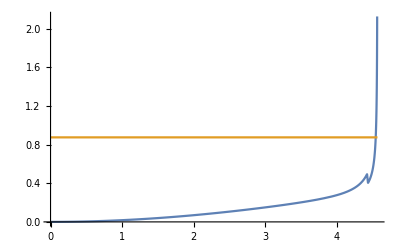

```mathematica
xpos =0.5;
Plot[{ 4π v^2 finterp[ψ[xpos] - 0.5*v^2]/ρDM[xpos], 4/vmax[xpos]}, {v, 0, vmax[xpos]}]
```

```mathematica
A^(1/2)
```

3784.34

```mathematica
sig[x_]:= Sqrt[ 4 π NIntegrate[v^4 finterp[ψ[x] - 0.5*v^2],{v, 0, vmax[x]}] /ρDM[x]]
```

```mathematica
N[Sqrt[3]]
N[Sqrt[4π]]
```

1.73205

3.54491

```mathematica
Print[sig[0.1]]
```

16.1183

```mathematica
Plot[ρDM[x], {x, 0.01, 5}]
```

-Graphics-

```mathematica
Plot[sig[x]/Sqrt[3], {x, 0.01, 5}, PlotRange->{0, 20}]
```

$Aborted

```mathematica
0.335/0.24
```

1.39583

```mathematica
0.11*1.396
```

0.15356

```mathematica
0.3354/0.2687
```

1.24823

```mathematica
10^-3/rtr
```

0.15873

```mathematica
ftab
```

{{0.,0.},{4.04835,9.88546×10^-9},{8.0967,1.78946×10^-6},{12.1451,0.0000374461},{16.1934,0.000323927},{20.2418,0.00172692},{24.2901,0.00677846},{28.3385,0.0215393},{32.3868,0.058637},{36.4352,0.141846},{40.4835,0.312606},{44.5319,0.638914},{48.5802,1.22703},{52.6286,2.23652},{56.6769,3.89904},{60.7253,6.54156},{64.7736,10.6144},{68.822,16.7249},{72.8703,25.6768},{76.9187,38.5167},{80.967,56.5877},{85.0154,81.5909},{89.0637,115.656},{93.1121,161.419},{97.1604,222.117},{101.209,301.68},{105.257,404.853},{109.305,537.31},{113.354,705.801},{117.402,918.294},{121.451,1184.15},{125.499,1514.29},{129.547,1921.42},{133.596,2420.2},{137.644,3027.53},{141.692,3762.77},{145.741,4648.},{149.789,5708.34},{153.837,6972.27},{157.886,8471.91},{158.886,8882.73},{159.412,9105.81},{159.938,9333.72},{160.465,9566.56},{160.991,9804.42},{161.517,10047.4},{162.044,10295.5},{162.57,10549.},{163.096,10808.8},{163.623,11068.7},{163.786,11142.},{163.986,0},{164.149,0},{164.675,0},{165.202,1762.48},{165.728,2915.59},{166.254,3645.12},{166.78,4170.},{167.307,4582.45},{167.833,4896.98},{168.359,5181.7},{168.886,5415.38},{169.886,5786.37},{210.526,10620.7},{260.889,12084.3},{323.3,12591.7},{400.641,12797.3},{496.484,12896.7},{615.254,12952.2},{762.438,12982.3},{944.831,13001.2},{1170.86,13014.2},{1450.95,13020.},{1798.05,13027.9},{2228.19,13032.4},{2761.23,13029.7},{3421.78,13034.9},{4240.35,13033.2},{5254.74,13030.8},{6511.8,13040.5},{8069.57,13038.6},{10000.,13041.4}}

```mathematica
Export[NotebookDirectory[] <> "Distribution_trunc.dat", ftab, "Table"]
```

/Users/bradkav/Projects/PBH_dress/PBHinDMclothing/code/distribution functions/Distribution_trunc.dat

### Solving Eddington’s Equation - v7

Hard Exponential cut off

```mathematica
ClearAll[A,B]
MPBH = 30;
rtr = 0.0063*(MPBH^(1/3));
G = 4.302 10^-3;
A = 3 MPBH/(8 π rtr^3);
B = G MPBH/rtr;
```

DM density profile

```mathematica
ClearAll[ρDM, α, β]
ρinner[x_]:= A x^(-3/2)
ρouter[x_]:=α Exp[-x/0.1]
ρDM[x_]:= Piecewise[{{ρinner[x], x < 1},{ρouter[x], x≥ 1}}]
s = Solve[ρinner[1] == ρouter[1] , {α}];
α = s[[All,1,2]][[1]]
```

1.05149×10^10

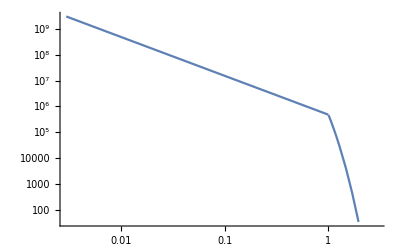

```mathematica
LogLogPlot[ρDM[x], {x, 0, 3}]
```

Potentials

```mathematica
ClearAll[ ψ, Minner, Mouter,Menc, ψouter, ψinner]
Minner[x_]:=MPBH (1+x^(3/2));
Mouter[x_]=2MPBH + rtr^3 Integrate[4 π ρouter[x1] x1^2, {x1, 1, x}];
Menc[x_] :=  Piecewise[{{Mouter[x], x >= 1},{Minner[x], x < 1}}]
ψouter[x_]= G Assuming[ x > 1, rtr^-1 Integrate[Mouter[x1]/x1^2, {x1, x, ∞}]];
ψinner[x_] = ψouter[1] + B(1 + x^-1 - 2 x^(1/2));
ψ[x_] := Piecewise[{{ψouter[x],x ≥1},{ψinner[x],x < 1}}]

ψouter[x]
ψtr = ψ[1]
ψmax = ψ[10^-5]
ψmin = ψ[5]
ρtr = ρDM[1];
```

0.219764 ((65.49+ⅇ^(-10. x) (-1982.38-9911.91 x))/x+3.63798×10^-12 Gamma[0,10. x])

14.2737

659312.

2.87847

```mathematica
ψouter[x]
```

```mathematica
ψtr
B
```

44.3516

20.4857

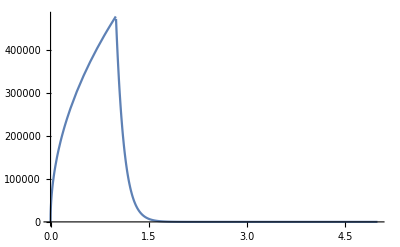

```mathematica
Plot[ρDM[x]x^2, {x, 0, 5}]
```

```mathematica
Menc[1] 
Menc[2]
Menc[3]
```

60.

65.4891

65.49

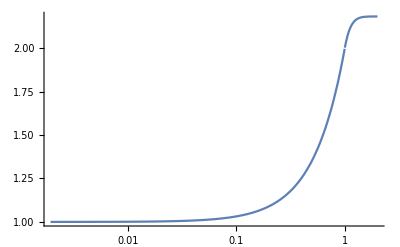

```mathematica
LogLinearPlot[Menc[x]/MPBH, {x, 0, 2}, PlotRange->All]
```

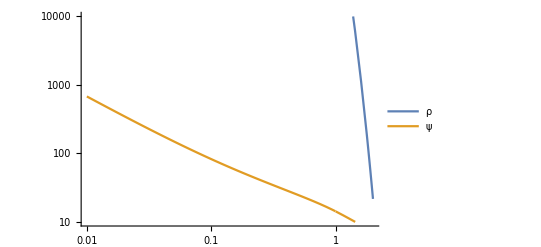

```mathematica
LogLogPlot[{ρDM[x], ψ[x]}, {x, 0.01, 2}, PlotLegends->{"ρ", "ψ"}, PlotRange->{10, 10^4}]
```

Inverting the potentials

```mathematica
ψinvOuter[ψ1_]= x/.Assuming[1 ≤ x && ψ1 ≥ 0 && B > 0 && ψ1 ∈ Reals && B ∈ Reals ,
Simplify[Solve[ψouter[x] == ψ1 ,x,Reals]]]
ψinvInner[ψ1_]=x/.Assuming[ψ1 ≥ 0 && B > 0 && ψ1 ∈ Reals && B ∈ Reals ,
Simplify[Solve[ψinner[x] == ψ1 ,x,Reals][[1]]]]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {Solve[(0.219764 (65.49+Power[«2»] Plus[«2»]))/x+7.99496×10^-13 Gamma[0,10. x]==ψ1,x,Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.Solve[(0.219764 (65.49+ⅇ^(-10. x) (-1982.38-9911.91 x)))/x+7.99496×10^-13 Gamma[0,10. x]==ψ1,x,Reals]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Root[-3.62775×10^45+(-2.29637×10^46+1.1005×10^45 ψ1) #1+(-3.634×10^46+3.48308×10^45 ψ1-8.34608×10^43 ψ1^2) #1^2+1.4511×10^46 #1^3&,1]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ψtr
```

24.174

```mathematica
l  = ψinvOuter[ψtr - 10]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-0.198958,0.520133,1.30118}

```mathematica
l[[3]]
```

26.9541

```mathematica
ψinv[ψ1_]:= Piecewise[{{Last[ψinvOuter[ψ1]], ψ1 < ψtr},{ψinvInner[ψ1], ψ1 ≥ ψtr}}]
ρofψ[ψ1_]:= If[ψ1 == 0, 0, ρDM[ψinv[ψ1]]]
```

```mathematica
ρofψ[10]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {Solve[(0.219764 (65.49+Power[«2»] Plus[«2»]))/x+7.99496×10^-13 Gamma[0,10. x]==10,x,Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Piecewise[{{477375./(Solve[(0.219764 (65.49+ⅇ^(-10. x) (-1982.38-9911.91 x)))/x+7.99496×10^-13 Gamma[0,10. x]==10,x,Reals]^(3/2)), Solve[(0.219764 (65.49+ⅇ^(-10. x) (-1982.38-9911.91 x)))/x+7.99496×10^-13 Gamma[0,10. x]==10,x,Reals]<1}, {1.05149×10^10 ⅇ^(-10. Solve[(0.219764 (65.49+ⅇ^(-10. x) (-1982.38-9911.91 x)))/x+7.99496×10^-13 Gamma[0,10. x]==10,x,Reals]), Solve[(0.219764 (65.49+ⅇ^(-10. x) (-1982.38-9911.91 x)))/x+7.99496×10^-13 Gamma[0,10. x]==10,x,Reals]≥1}, {0, True}}]

```mathematica
LogLogPlot[ρofψ[ψ1 ], {ψ1, ψmin, ψmax}, PlotPoints->2]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {Solve[(0.219764 (65.49+Power[«2»] Plus[«2»]))/x+7.99496×10^-13 Gamma[0,10. x]==2.91425,x,Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

General::stop: Further output of Solve::inex will be suppressed during this calculation.

$Aborted

```mathematica
ρofψ[ψtr]
```

1.43213×10^7

```mathematica
ψmin
ψmax
```

2.04864×10^6

8.94406

```mathematica
ψvals = DeleteDuplicates[Flatten[{0,10^Linspace[-3, Log10[0.949ψtr], 1000],Linspace[0.95 ψtr, 1.05 ψtr, 1000],10^Linspace[Log10[1.051 ψtr],Log10[ψmax],1000]}]];
ρtab = Table[{ψ1,ρofψ[ψ1]}, {ψ1,ψvals}];
ListLogLogPlot[ρtab]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {Solve[(0.219764 (65.49+Power[«2»] Plus[«2»]))/x+7.99496×10^-13 Gamma[0,10. x]==0.001,x,Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {Solve[(0.219764 (65.49+Power[«2»] Plus[«2»]))/x+7.99496×10^-13 Gamma[0,10. x]==0.00100957,x,Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

General::stop: Further output of Solve::inex will be suppressed during this calculation.

ReplaceAll::reps: {Solve[(0.219764 (65.49+Power[«2»] Plus[«2»]))/x+7.99496×10^-13 Gamma[0,10. x]==0.00101923,x,Reals]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

General::stop: Further output of Solve::inex will be suppressed during this calculation.

$Aborted

```mathematica
ρofψinterp = Interpolation[ρtab];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

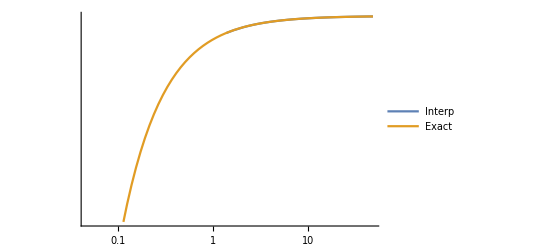

```mathematica
LogLogPlot[{ρofψinterp[ψ1], ρofψ[ψ1]}, {ψ1,0,  ψtr + 4}, PlotPoints->2, PlotLegends->{"Interp", "Exact"}]
```

Asymptotic derivatives

```mathematica
ClearAll[dρAsymp, d2ρAsymp]
dρAsymp[ψ1_]:= (3/2)A (ψ1 - (B+ ψ[1]))^(1/2)/B^(3/2)
d2ρAsymp[ψ1_]:= (3/4)A (ψ1-(B + ψ[1]))^(-1/2)/B^(3/2)
```

```mathematica
ClearAll[d2ρ]
δ = 0.25;
d2ρ[ψ1_]:= Piecewise[{
{ND[ρofψinterp[a], {a, 2}, ψtr -δ], ψtr -δ < ψ1 < ψtr},
{ND[ρofψinterp[a], {a, 2}, ψtr +δ], ψtr < ψ1 < ψtr+δ},
{ND[ρofψinterp[a], {a, 2}, ψ1], ψ1 < 1000ψtr},
{d2ρAsymp[ψ1], ψ1 ≥1000 ψtr}}
]
```

```mathematica
d2ρ[10]
```

2.246×10^-7

```mathematica
ND[ρofψinterp[a], {a, 2}, ψtr -0.5]
ND[ρofψinterp[a], {a, 2}, ψtr -0.25]
ND[ρofψinterp[a], {a, 2}, ψtr +0.5]
ND[ρofψinterp[a], {a, 2}, ψtr +0.25]
```

678067.

631536.

16102.3

16049.7

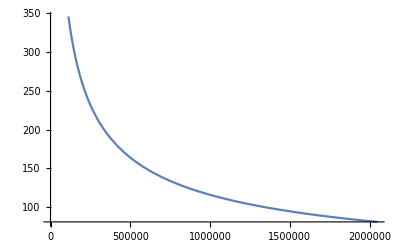

```mathematica
Plot[d2ρAsymp[ψ1],{ψ1, ψtr, ψmax}]
```

```mathematica
B
ψtr
```

20.4857

44.3516

```mathematica
d2ρ[0.1]
```

-6.9586×10^-9

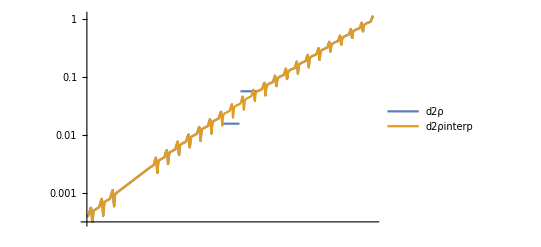

```mathematica
LogLogPlot[{d2ρ[ψ1],ND[ρofψinterp[a], {a, 2}, ψ1]}, {ψ1,ψtr-2,ψtr+2}, PlotPoints->10, PlotLegends-> {"d2ρ", "d2ρinterp"}]
```

```mathematica
ND[ρofψinterp[a], {a, 2}, 6 ψtr]/d2ρAsymp[6 ψtr]
LogPlot[{ND[ρofψinterp[a], {a, 2}, ψ1 ψtr],d2ρAsymp[ψ1 ψtr]} , {ψ1, 1, 100.0}, PlotPoints->2]
```

0.998723

Power::infy: Infinite expression 1/(√0.) encountered.

-Graphics-

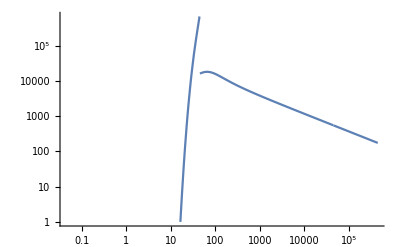

```mathematica
LogLogPlot[d2ρ[ψ1 ], {ψ1, ψtr*0.001, ψtr*10000}]
```

Calculating the discontinuity as x = 1

```mathematica
dinner = D[ρinner[x], x]/D[ψinner[x],x]/.x->1
douter = D[ρouter[x], x]/D[ψouter[x],x]/.x->1
jump = -douter + dinner
```

54305.5

362037.

-307731.

```mathematica
ρp = D[ρinner[x], x];
ρpp =  D[ρinner[x], {x,2}];
ψp = D[ψinner[x],x];
ψpp = D[ψinner[x],{x,2}];
```

```mathematica
d2inner = ((ρpp/(ψp^2)) - (ψp^-3)ρp ψpp)/.x->1
```

5148.09

```mathematica
(*15996.319118109905*)
(*746494.8921784625*)
```

```mathematica
(*jump = ND[ρofψinterp[a], {a, 2}, ψtr + δ] - ND[ρofψinterp[a], {a, 2}, ψtr -δ]*)
```

-615486.

```mathematica
ClearAll[f];
f[ϵ_]:=
(1/(Sqrt[8] π^2))(NIntegrate[d2ρ[ψ1]/Sqrt[ϵ - ψ1], {ψ1, 0, ϵ}]); (*Add step function!*)
```

```mathematica
f[ψtr]
f[ψtr*5]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {37.4684}. NIntegrate obtained 2.78458×10^6-5.92823×10^-8 ⅈ and 157.998 for the integral and error estimates.

99750.6

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {38.6743}. NIntegrate obtained 573530.+0. ⅈ and 88.124 for the integral and error estimates.

18889.9

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {46.6018}. NIntegrate obtained 415119.-1.45352×10^-12 ⅈ and 8850.62 for the integral and error estimates.

13264.4

```mathematica
ψ[10]
```

10.6981

```mathematica
f[0]
```

0.

```mathematica
ψmin
ψmax
ψtr
```

4.47203

2.04864×10^6

44.3516

```mathematica
ϵmin = ψmin; ϵmax = ψmax;
ϵvals =Sort[N[DeleteDuplicates[Flatten[{0,10^Linspace[-2,Log10[ψtr], 100],Linspace[0.9 ψtr, 1.10 ψtr, 50], 10^Linspace[Log10[ψtr], Log10[ψmax],50]}]]]]
(*ϵvals = Linspace[ψtr - 5, ψtr + 5, 50];*)
ftab = Table[{ϵ, Clip [Re[f[ϵ]], {0, 10^30}]}, {ϵ, ϵvals}];
finterp = Interpolation[ftab, InterpolationOrder->1];
```

{0.,0.01,0.0108852,0.0118488,0.0128977,0.0140394,0.0152823,0.0166351,0.0181077,0.0197106,0.0214554,0.0233547,0.0254221,0.0276726,0.0301222,0.0327887,0.0356913,0.0388508,0.0422899,0.0460335,0.0501085,0.0545443,0.0593727,0.0646285,0.0703496,0.0765771,0.083356,0.0907348,0.0987669,0.10751,0.117027,0.127387,0.138663,0.150938,0.1643,0.178844,0.194675,0.211909,0.230667,0.251087,0.273314,0.297508,0.323844,0.352512,0.383717,0.417685,0.454659,0.494907,0.538717,0.586406,0.638316,0.694821,0.756329,0.823281,0.89616,0.975491,1.06184,1.15584,1.25816,1.36953,1.49077,1.62274,1.76638,1.92275,2.09296,2.27823,2.47991,2.69943,2.93839,3.19851,3.48165,3.78985,4.12534,4.49053,4.88804,5.32074,5.79175,6.30445,6.86254,7.47003,8.13129,8.8511,9.63462,10.4875,11.4159,12.4264,13.5265,14.7239,16.0273,17.446,18.9904,20.6715,22.5014,24.4933,26.6615,29.0216,31.5907,34.3872,37.4312,39.9164,40.0974,40.2785,40.4595,40.6405,40.7447,40.8215,41.0026,41.1836,41.3646,41.5457,41.7267,41.9077,42.0887,42.2698,42.4508,42.6318,42.8128,42.9939,43.1749,43.3559,43.537,43.718,43.899,44.08,44.2611,44.3516,44.3516,44.4421,44.6231,44.8041,44.9852,45.1662,45.3472,45.5282,45.7093,45.8903,46.0713,46.2524,46.4334,46.6144,46.7954,46.9765,47.1575,47.3385,47.5195,47.7006,47.8816,48.0626,48.2436,48.4247,48.6057,48.7867,55.221,68.7542,85.604,106.583,132.704,165.226,205.719,256.135,318.907,397.063,494.372,615.53,766.38,954.2,1188.05,1479.21,1841.72,2293.08,2855.05,3554.75,4425.93,5510.61,6861.11,8542.59,10636.1,13242.8,16488.2,20529.1,25560.2,31824.3,39623.7,49334.4,61424.9,76478.5,95221.4,118558.,147613.,183789.,228831.,284911.,354736.,441672.,549914.,684683.,852481.,1.0614×10^6,1.32152×10^6,1.64539×10^6,2.04864×10^6}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {0.025422140374024720758605328566432023291916903271774818786659096517}. NIntegrate obtained 1.26817×10^-95+1.42212×10^-100 ⅈ and 2.04832×10^-100 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {0.106283}. NIntegrate obtained 2.87285×10^-88 and 5.6996×10^-93 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {0.106237}. NIntegrate obtained 3.0641×10^-87 and 3.18462×10^-93 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ftab
```

{{0.,0.},{0.001,0},{0.00124404,0},{0.00154764,0},{0.00192533,0},{0.00239519,0},{0.00297971,0},{0.00370689,0},{0.00461152,0},{0.00573692,0},{0.00713697,0},{0.00887869,0},{0.0110455,4.23312×10^-95},{0.013741,3.04662×10^-94},{0.0170944,9.02237×10^-94},{0.0212661,9.38844×10^-94},{0.0264559,0},{0.0329123,1.48171×10^-93},{0.0409443,1.37126×10^-92},{0.0509363,2.23113×10^-93},{0.0633669,1.42427×10^-91},{0.0788311,4.55369×10^-91},{0.0980692,2.08781×10^-90},{0.122002,3.39888×10^-89},{0.151776,1.36237×10^-87},{0.188815,2.25675×10^-86},{0.234894,1.71578×10^-84},{0.292218,4.95417×10^-82},{0.363531,1.67554×10^-79},{0.452248,1.58838×10^-76},{0.562615,4.4151×10^-73},{0.699917,3.7823×10^-69},{0.870725,8.93827×10^-65},{1.08322,4.29052×10^-60},{1.34757,4.48574×10^-55},{1.67643,7.97386×10^-50},{2.08555,1.76821×10^-44},{2.59451,3.69984×10^-39},{3.22768,5.56821×10^-34},{4.01537,4.70495×10^-29},{4.99528,1.81148×10^-24},{6.21434,8.2969×10^-20},{7.7309,2.74881×10^-14},{9.61756,1.35306×10^-9},{11.9646,6.1436×10^-6},{14.8845,0.00500512},{18.517,0.924372},{23.0359,55.2386},{28.6576,1282.62},{33.2637,7148.},{33.7162,8202.96},{34.1688,9414.37},{34.6214,10759.6},{35.0739,12263.6},{35.5265,13887.4},{35.6512,14378.7},{35.9791,15713.},{36.4316,17720.9},{36.8842,19926.8},{37.3368,22344.8},{37.7893,25007.5},{38.2419,27843.9},{38.6945,31024.7},{39.1471,34479.8},{39.5996,38224.9},{40.0522,42324.9},{40.5048,46750.5},{40.9573,51591.9},{41.4099,56824.4},{41.8625,62514.},{42.315,68716.7},{42.7676,75465.6},{43.2202,82802.2},{43.6727,90818.7},{44.1253,97093.2},{44.3516,99750.6},{44.3516,99750.6},{44.5779,34978.3},{45.0304,44072.9},{45.483,44154.8},{45.9356,43143.6},{46.3881,41954.6},{46.8407,40795.8},{47.2933,39715.3},{47.7458,38723.},{48.1984,37815.1},{48.651,36984.7},{49.1035,36223.1},{49.5561,35523.1},{50.0087,34878.},{50.4612,34281.3},{50.9138,33728.3},{51.3664,33213.6},{51.8189,32734.6},{52.2715,32270.1},{52.7241,31851.1},{53.1766,31457.8},{53.6292,31087.7},{54.0818,30739.5},{54.5343,30410.8},{54.9869,30100.5},{55.221,29946.6},{55.4395,29806.5},{68.7542,25131.6},{85.604,23025.8},{106.583,21741.9},{132.704,20746.6},{165.226,19888.7},{205.719,19129.4},{256.135,18456.6},{318.907,17859.7},{397.063,17332.7},{494.372,16866.5},{615.53,16456.5},{766.38,16086.8},{954.2,15762.7},{1188.05,15473.7},{1479.21,15216.2},{1841.72,14986.8},{2293.08,14782.},{2855.05,14599.2},{3554.75,14435.7},{4425.93,14289.7},{5510.61,14159.1},{6861.11,14042.2},{8542.59,13937.3},{10636.1,13843.7},{13242.8,13759.4},{16488.2,13684.4},{20529.1,13618.},{25560.2,13558.3},{31824.3,13504.7},{39623.7,13456.},{49334.4,13412.2},{61424.9,13373.2},{76478.5,13338.2},{95221.4,13306.9},{118558.,13278.8},{147613.,13253.6},{183789.,13231.1},{228831.,13210.9},{284911.,13192.8},{354736.,13176.6},{441672.,13162.1},{549914.,13149.1},{684683.,13137.4},{852481.,13127.},{1.0614×10^6,13117.6},{1.32152×10^6,13109.2},{1.64539×10^6,13101.7},{2.04864×10^6,13095.}}

```mathematica
100000/ψtr
```

1331.3

```mathematica
finterp = Interpolation[ftab, InterpolationOrder->1]
f2[ϵ_] := finterp[ϵ] +   (1/(Sqrt[8] π^2))If[ϵ > ψtr, jump/Sqrt[ϵ - ψtr],0]
```

6
InterpolatingFunction[{{0., 2.04864 10 }}, <>]

```mathematica
ftab2 = Table[{ϵ, Clip [f2[ϵ], {0, 10^30}]}, {ϵ, ϵvals}];
```

```mathematica
ftab
```

{{0.,0.},{0.24174,6.5016×10^-12},{0.265562,8.40151×10^-12},{0.29173,1.10552×10^-11},{0.320478,1.4828×10^-11},{0.352058,2.02918×10^-11},{0.38675,2.83564×10^-11},{0.424861,4.04951×10^-11},{0.466727,5.91342×10^-11},{0.512719,8.83379×10^-11},{0.563243,1.35025×10^-10},{0.618746,2.1115×10^-10},{0.679717,3.37623×10^-10},{0.746698,5.51289×10^-10},{0.820278,9.16961×10^-10},{0.901109,1.54649×10^-9},{0.989905,2.62284×10^-9},{1.08745,4.40917×10^-9},{1.19461,7.17718×10^-9},{1.31233,1.10489×10^-8},{1.44165,1.90332×10^-8},{1.58371,1.00501×10^-7},{1.73977,1.20637×10^-6},{1.91121,0.0000129019},{2.09954,0.000109597},{2.30643,0.000748743},{2.53371,0.00419474},{2.78338,0.0196185},{3.05766,0.0778486},{3.35897,0.265901},{3.68997,0.792731},{4.05358,2.0871},{4.45302,4.91011},{4.89183,10.4292},{5.37388,20.2015},{5.90342,36.0309},{6.48515,59.7131},{7.12421,92.7787},{7.82623,136.275},{8.59744,190.697},{9.44464,256.019},{10.3753,331.743},{11.3977,416.959},{12.5209,510.188},{13.7547,608.992},{15.1101,709.227},{16.5991,803.645},{18.2347,880.242},{20.0316,920.648},{22.0056,902.043},{24.174,807.661},{27.8338,1343.65},{32.0478,1637.91},{36.8997,1865.72},{42.4861,2029.38},{48.9183,2140.69},{56.3243,2214.66},{64.8515,2263.8},{74.6698,2296.88},{85.9744,2319.59},{98.9905,2335.42},{113.977,2346.75},{131.233,2354.92},{151.101,2360.51},{173.977,2364.9},{200.316,2368.45},{230.643,2370.99},{265.562,2373.26},{305.766,2374.77},{352.058,2375.93},{405.358,2376.83},{466.727,2377.54},{537.388,2378.09},{618.746,2378.53},{712.421,2378.88},{820.278,2379.15},{944.464,2379.37},{1087.45,2379.54},{1252.09,2379.68},{1441.65,2379.79},{1659.91,2379.87},{1911.21,2379.94},{2200.56,2380.},{2533.71,2380.04},{2917.3,2380.08},{3358.97,2380.11},{3867.5,2380.13},{4453.02,2380.14},{5127.19,2380.16},{5903.42,2380.17},{6797.17,2380.18},{7826.23,2380.18},{9011.09,2380.19},{10375.3,2380.19},{11946.1,2380.19},{13754.7,2380.19},{15837.1,2380.19},{18234.7,2380.2},{20995.4,2380.2},{24174.,2380.2},{241740.,2380.19}}

```mathematica
ψtr
```

44.3516

```mathematica
f[ψtr*1.005]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ψ1 near {ψ1} = {37.4684}. NIntegrate obtained 2.27479×10^6-5.45721×10^-7 ⅈ and 155.351 for the integral and error estimates.

34668.3

```mathematica
(*f2[ϵ_]:= Clip[finterp[ϵ] - If[ϵ > ψtr,5*34668.29039275575/Sqrt[ϵ - ψtr],0], {0, 10^30}]*)
```

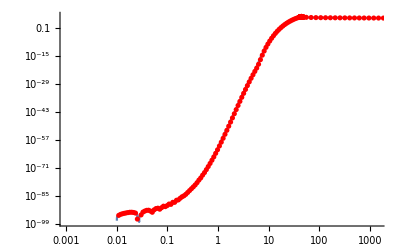

```mathematica
Show[LogLogPlot[finterp[ϵ], {ϵ,10^-3, 100 ψtr}], ListLogLogPlot[ftab, PlotStyle->Red]]
```

```mathematica
ClearAll[vmax]
vmax[xpos_]:= Sqrt[ 2 (ψ[xpos] )];
```

```mathematica
Dens[xpos_]:= 4 π NIntegrate[v^2 f2[ψ[xpos] - 0.5*v^2], {v,0, vmax[xpos]}]
```

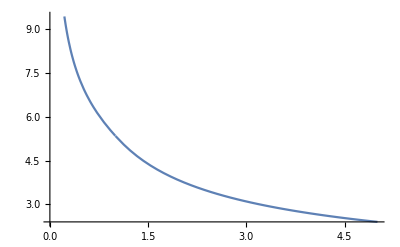

```mathematica
Plot[vmax[xpos], {xpos, 0.01, 5}]
```

```mathematica
xpos = 0.1
ψ[xpos]
Dens[xpos]
ρDM[xpos]
```

0.1

82.626

-4.13693×10^7+0.995948 ⅈ

1.50959×10^7

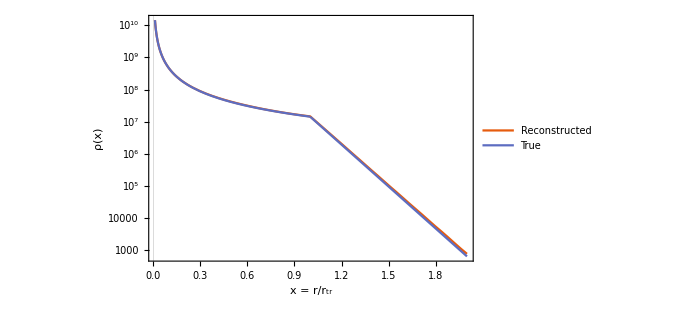

```mathematica
LogPlot[{ Dens[x], ρDM[x]}, {x, 0.01, 2}, PlotRange-> All, PlotLegends->{"Reconstructed", "True"},
 PlotTheme->"Scientific", FrameLabel->{"x = r/r_tr", "ρ(x)"}, ImageSize->500]
```

```mathematica
LogPlot[{ Dens[x]/ρDM[x]}, {x, 0.01, 2}, PlotRange-> All,
 PlotTheme->"Scientific", FrameLabel->{"x = r/r_tr", "ρ_recon(x)/ρ_true(x)"}, ImageSize->500]
```

$Aborted

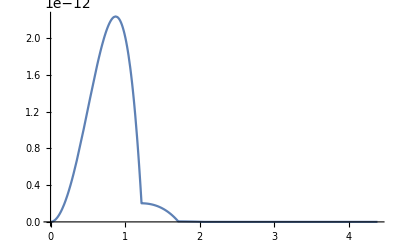

```mathematica
xpos =;
Plot[{ 4π v^2 f2[ψ[xpos] - 0.5*v^2]/ρDM[xpos]}, {v, 0, vmax[xpos]}]
```

```mathematica
A^(1/2)
```

3784.34

```mathematica
sig[x_]:= Sqrt[ 4 π NIntegrate[v^4 finterp[ψ[x] - 0.5*v^2],{v, 0, vmax[x]}] /ρDM[x]]
```

```mathematica
N[Sqrt[3]]
N[Sqrt[4π]]
```

1.73205

3.54491

```mathematica
Print[sig[0.1]]
```

16.1183

```mathematica
Plot[ρDM[x], {x, 0.01, 5}]
```

-Graphics-

```mathematica
Plot[sig[x]/Sqrt[3], {x, 0.01, 5}, PlotRange->{0, 20}]
```

$Aborted

```mathematica
10^-3/rtr
```

0.15873

```mathematica
ftab
```

{{0.,0.},{4.04835,9.88546×10^-9},{8.0967,1.78946×10^-6},{12.1451,0.0000374461},{16.1934,0.000323927},{20.2418,0.00172692},{24.2901,0.00677846},{28.3385,0.0215393},{32.3868,0.058637},{36.4352,0.141846},{40.4835,0.312606},{44.5319,0.638914},{48.5802,1.22703},{52.6286,2.23652},{56.6769,3.89904},{60.7253,6.54156},{64.7736,10.6144},{68.822,16.7249},{72.8703,25.6768},{76.9187,38.5167},{80.967,56.5877},{85.0154,81.5909},{89.0637,115.656},{93.1121,161.419},{97.1604,222.117},{101.209,301.68},{105.257,404.853},{109.305,537.31},{113.354,705.801},{117.402,918.294},{121.451,1184.15},{125.499,1514.29},{129.547,1921.42},{133.596,2420.2},{137.644,3027.53},{141.692,3762.77},{145.741,4648.},{149.789,5708.34},{153.837,6972.27},{157.886,8471.91},{158.886,8882.73},{159.412,9105.81},{159.938,9333.72},{160.465,9566.56},{160.991,9804.42},{161.517,10047.4},{162.044,10295.5},{162.57,10549.},{163.096,10808.8},{163.623,11068.7},{163.786,11142.},{163.986,0},{164.149,0},{164.675,0},{165.202,1762.48},{165.728,2915.59},{166.254,3645.12},{166.78,4170.},{167.307,4582.45},{167.833,4896.98},{168.359,5181.7},{168.886,5415.38},{169.886,5786.37},{210.526,10620.7},{260.889,12084.3},{323.3,12591.7},{400.641,12797.3},{496.484,12896.7},{615.254,12952.2},{762.438,12982.3},{944.831,13001.2},{1170.86,13014.2},{1450.95,13020.},{1798.05,13027.9},{2228.19,13032.4},{2761.23,13029.7},{3421.78,13034.9},{4240.35,13033.2},{5254.74,13030.8},{6511.8,13040.5},{8069.57,13038.6},{10000.,13041.4}}

```mathematica
Export[NotebookDirectory[] <> "Distribution_trunc.dat", ftab2, "Table"]
```

/Users/bradkav/Projects/PBH_dress/PBHinDMclothing/code/distribution functions/Distribution_trunc.dat